# Linear arrangement AXM

## life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with female and male-specific meiotic drive (individuals of sex i who are heterozygous at the viablilty locus produce α_i% A haplotypes and 1-α_i% a haplotypes before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->Subscript[α, male](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->Subscript[α, male]((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] (r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->Subscript[α, male] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] (r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] ((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) ((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,A,z1_]->Subscript[α, female](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z1_]->Subscript[α, female]((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] (r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,A,z1_]->Subscript[α, female] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z1_]->Subscript[α, female](r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(r(1-χ)+(1-r)χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] ((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) ((1-r)(1-χ)+r χ),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-χ)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-χ)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->χ/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->χ/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-r)(1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-r)(1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] r χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])r χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] r (1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) r (1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male](1-r)χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male]  r (1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male]) r (1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] (1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-r)(1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-r)(1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] r χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male]) r χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-r)(1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-r)(1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] r χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])r χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] r (1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) r (1-χ),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female](1-r)χ,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female]  r (1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female]) r (1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] (1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-r)χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-r)(1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-r)(1-χ),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] r χ,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female]) r χ
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## find resident equilibrium

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

Shorten expressions up with some substitutions and copy and paste into function to find equibria

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
differenceEqs/.varsub//Simplify
```

{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}

```mathematica
Clear[equilAXM]
equilAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveAXM]
sieveAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilAXM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

## characteristic polynomial

The characteristic polynomial for invasion into XY is

```mathematica
(*eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
jac=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
detjac=Det[jac-IdentityMatrix[8]*λ];*)
```

And for a neo-W this reduces to

```mathematica
(*detjac/.k->1/.varsub*)
```

```mathematica
detjack1=(λ^2 (2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) (-1+r) χ (2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma (-r+pXm r-freqYm pXm r+freqYm pYm r-freqYm χ+freqYm pYm χ+r χ+freqYm r χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))-(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pYm-2 FAa MA pYm r+2 FAa FdA MA pYm r) χ (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ+(Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+2 FAa MA pXm r-2 FAa FdA MA pXm r-2 FAa freqYm MA pXm r+2 FAa FdA freqYm MA pXm r+2 FAa freqYm MA pYm r-2 FAa FdA freqYm MA pYm r+Faa Ma χ-Faa freqYm Ma χ-Faa Ma pXm χ+Faa freqYm Ma pXm χ+2 FAa MA pXm χ-2 FAa FdA MA pXm χ-2 FAa freqYm MA pXm χ+2 FAa FdA freqYm MA pXm χ+2 FAa freqYm MA pYm χ-2 FAa FdA freqYm MA pYm χ-2 FAa MA pXm r χ+2 FAa FdA MA pXm r χ+2 FAa freqYm MA pXm r χ-2 FAa FdA freqYm MA pXm r χ-4 FAa freqYm MA pYm r χ+4 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2);
```

Unfortunately we can’t seem to reduce this any farther, even with no drive, so we will just use the whole expression in the invasion fitness function

```mathematica
(*detjack1/.MdA->1/2/.FdA->1/2/.freqYm->1/2(*/.FA->1/.Fa->1/.MA->1/.Ma->1/.Faa->1/.FAa->1/.FAA->1/.Maa->1/.MAa->1/.MAA->1*)//Factor*)
```

$Aborted

## invasion function [only need this]

Resident equilibria

```mathematica
Clear[equilAXM]
equilAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveAXM]
sieveAXM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilAXM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotAXM]
invasionplotAXM[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
r=tryr,
χ=tryχ
},
Max[λ/.NSolve[0==((λ^2 (2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) (-1+r) χ (2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma (-r+pXm r-freqYm pXm r+freqYm pYm r-freqYm χ+freqYm pYm χ+r χ+freqYm r χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))-(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pYm-2 FAa MA pYm r+2 FAa FdA MA pYm r) χ (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (pXm r-freqYm pXm r+freqYm pYm r+freqYm pYm χ-pXm r χ+freqYm pXm r χ-2 freqYm pYm r χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm r+2 FAa FdA MA pXm r) χ (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ+(Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+2 FAa MA pXm r-2 FAa FdA MA pXm r-2 FAa freqYm MA pXm r+2 FAa FdA freqYm MA pXm r+2 FAa freqYm MA pYm r-2 FAa FdA freqYm MA pYm r+Faa Ma χ-Faa freqYm Ma χ-Faa Ma pXm χ+Faa freqYm Ma pXm χ+2 FAa MA pXm χ-2 FAa FdA MA pXm χ-2 FAa freqYm MA pXm χ+2 FAa FdA freqYm MA pXm χ+2 FAa freqYm MA pYm χ-2 FAa FdA freqYm MA pYm χ-2 FAa MA pXm r χ+2 FAa FdA MA pXm r χ+2 FAa freqYm MA pXm r χ-2 FAa FdA freqYm MA pXm r χ-4 FAa freqYm MA pYm r χ+4 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-2 FA FAa (-1+FdA) Ma (r-pXm r+freqYm pXm r-freqYm pYm r+χ-freqYm χ-pXm χ+freqYm pXm χ-2 r χ+freqYm r χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) χ (-8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ (-pXm r+freqYm pXm r-freqYm pYm r-pXm χ+freqYm pXm χ+2 pXm r χ-2 freqYm pXm r χ+freqYm pYm r χ)-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm r+2 FAa FdA MA pXm r+2 FAa freqYm MA pXm r-2 FAa FdA freqYm MA pXm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma χ-2 FAa MA pXm χ+2 FAa FdA MA pXm χ+2 FAa freqYm MA pXm χ-2 FAa FdA freqYm MA pXm χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+4 FAa MA pXm r χ-4 FAa FdA MA pXm r χ-4 FAa freqYm MA pXm r χ+4 FAa FdA freqYm MA pXm r χ+2 FAa freqYm MA pYm r χ-2 FAa FdA freqYm MA pYm r χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-FAA MA pXm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r) (-FAA MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pYm r) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r+2 FAa FdA freqYm Ma pYm r-2 FAa FdA Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA freqYm Ma pYm χ+2 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ-2 FAa FdA Ma pXm r χ+2 FAa FdA freqYm Ma pXm r χ-4 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma r-2 FAa FdA Ma pXm r+2 FAa FdA freqYm Ma pXm r-2 FAa FdA freqYm Ma pYm r+2 FAa FdA Ma χ-2 FAa FdA Ma pXm χ+2 FAa FdA freqYm Ma pXm χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-4 FAa FdA Ma r χ+2 FAa FdA freqYm Ma r χ+4 FAa FdA Ma pXm r χ-4 FAa FdA freqYm Ma pXm r χ+2 FAa FdA freqYm Ma pYm r χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2))/.subs,λ]]-1
]
```

## mapping functions

Mapping functions

```mathematica
setr[x_,a_]:=(1-Exp[-2 √((x-a)^2)])/2
setR[a_,m_]:=(1-Exp[-2 √((a-m)^2)])/2
setχ[x_,m_]:=(1-Exp[-2 √((x-m)^2)])/2
```

## parameters

Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

## plot

test

```mathematica
x=-0.05;
a=-0.06;
m=0.05;

setr[x,a]
setR[a,m]
setχ[x,m]

Flatten[sieveAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]]

invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]
```

0.00990066

0.0987406

0.0906346

{0.689149,0.70276,0.140891,0.5}

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.0181467

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

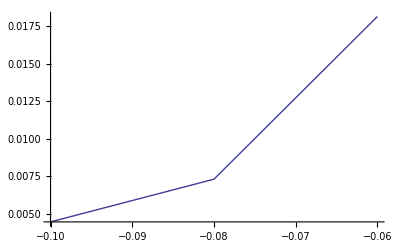

```mathematica
x=-0.05;
m=0.05;
Clear[a]
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.1,-0.06,0.02}],Joined->True]
```

# Linear arrangement XAM

## life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with female and male-specific meiotic drive (individuals of sex i who are heterozygous at the viablilty locus produce α_i% A haplotypes and 1-α_i% a haplotypes before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->Subscript[α, male](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->Subscript[α, male] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,A,z1_]->Subscript[α, female](1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])r,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,A,z1_]->Subscript[α, female] (1-r),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-r),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->((1-r)(1-R)+r R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->(r(1-R)+(1-r)R)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->(r(1-R)+(1-r)R)/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male](1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])r (1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-r)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])r(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) r R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female](1-r)R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])r R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] (1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-r)R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-r)(1- R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] r(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])r (1-R)
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

```mathematica
(*ParallelSum[Subscript[fHapNext, x,y,z,sex]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4,{x,{X,Y}},{y,{A,a}},{z,{M,m}},{sex,{male,female}}]//Factor*)
```

## find resident equilibrium

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

Shorten expressions up with some substitutions and copy and paste into function to find equibria

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
differenceEqs/.varsub//Simplify
```

{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}

```mathematica
Clear[equilXAM]
equilXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXAM]
sieveXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXAM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

## characteristic polynomial

The characteristic polynomial for invasion into XY is

```mathematica
(*eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
jac=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
detjac=Det[jac-IdentityMatrix[8]*λ];*)
```

And for a neo-W this reduces to

```mathematica
(*detjac/.k->1/.varsub*)
```

```mathematica
detjack1=(λ^2 (2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) (-1+r) R (2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 R^2 λ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) (-pXm+freqYm pXm-freqYm pYm r) R^2 λ^2)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma (-freqYm+freqYm pYm-r+freqYm r+pXm r-freqYm pXm r) R (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r)^2 R^2 λ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) (-pXm+freqYm pXm-freqYm pYm r) R^2 λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))+(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pYm r+2 FAa MA pYm r-2 FAa FdA MA pYm r+Faa Ma R-Faa Ma pYm R-2 Faa Ma r R+2 Faa Ma pYm r R-2 FAa MA pYm r R+2 FAa FdA MA pYm r R) (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2-16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (freqYm pYm+pXm r-freqYm pXm r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (Faa Ma r-Faa Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r+Faa Ma R-Faa Ma pXm R-2 Faa Ma r R+2 Faa Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) ((Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+Faa Ma r-Faa freqYm Ma r-Faa Ma pXm r+Faa freqYm Ma pXm r+2 FAa MA pXm r-2 FAa FdA MA pXm r-2 FAa freqYm MA pXm r+2 FAa FdA freqYm MA pXm r+Faa Ma R-Faa freqYm Ma R-Faa Ma pXm R+Faa freqYm Ma pXm R+2 FAa MA pXm R-2 FAa FdA MA pXm R-2 FAa freqYm MA pXm R+2 FAa FdA freqYm MA pXm R+2 FAa freqYm MA pYm R-2 FAa FdA freqYm MA pYm R-2 Faa Ma r R+2 Faa freqYm Ma r R+2 Faa Ma pXm r R-2 Faa freqYm Ma pXm r R-2 FAa MA pXm r R+2 FAa FdA MA pXm r R+2 FAa freqYm MA pXm r R-2 FAa FdA freqYm MA pXm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (-2 FA FAa (-1+FdA) Ma (1-freqYm-pXm+freqYm pXm+freqYm r-freqYm pYm r) R (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) λ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) (-1+r) R (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-pXm+freqYm pXm-freqYm pYm r) R (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2-16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (-1+r) R (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-Faa freqYm Ma r+Faa freqYm Ma pYm r-2 FAa freqYm MA pYm r+2 FAa FdA freqYm MA pYm r-Faa freqYm Ma R-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R+Faa freqYm Ma pYm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R+2 Faa freqYm Ma r R-2 Faa freqYm Ma pYm r R+2 FAa freqYm MA pYm r R-2 FAa FdA freqYm MA pYm r R))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))-λ) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma r-2 FAa FdA Ma pXm r+FAA MA pXm r+FAA MA pXm R-2 FAa FdA Ma r R+2 FAa FdA Ma pXm r R-2 FAA MA pXm r R) (2 FAa FdA Ma r-2 FAa FdA Ma pYm r+FAA MA pYm r+FAA MA pYm R-2 FAa FdA Ma r R+2 FAa FdA Ma pYm r R-2 FAA MA pYm r R) λ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 ((FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma r+2 FAa FdA freqYm Ma r+2 FAa FdA Ma pXm r-2 FAa FdA freqYm Ma pXm r-FAA MA pXm r+FAA freqYm MA pXm r-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R-FAA MA pXm R+FAA freqYm MA pXm R+2 FAa FdA freqYm Ma pYm R+2 FAa FdA Ma r R-2 FAa FdA freqYm Ma r R-2 FAa FdA Ma pXm r R+2 FAa FdA freqYm Ma pXm r R+2 FAA MA pXm r R-2 FAA freqYm MA pXm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) (-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA freqYm Ma r-2 FAa FdA freqYm Ma pYm r+FAA freqYm MA pYm r+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+FAA freqYm MA pYm R-2 FAa FdA freqYm Ma r R+2 FAa FdA freqYm Ma pYm r R-2 FAA freqYm MA pYm r R))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))-λ) λ^2))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2);
```

If there is no meiotic drive this reduces further and can be factored

```mathematica
(*detjack1/.MdA->1/2/.FdA->1/2/.freqYm->1/2//Factor*)
```

```mathematica
detjack1nodrive=(λ^4 (4 Fa FA Faa FAa Ma^2-4 Fa FA Faa FAa Ma^2 pXm+2 Fa FA FAa^2 Ma MA pXm+2 Fa FA Faa FAA Ma MA pXm+Fa FA Faa FAa Ma^2 pXm^2-Fa FA FAa^2 Ma MA pXm^2-Fa FA Faa FAA Ma MA pXm^2+Fa FA FAa FAA MA^2 pXm^2-4 Fa FA Faa FAa Ma^2 pYm+2 Fa FA FAa^2 Ma MA pYm+2 Fa FA Faa FAA Ma MA pYm+2 Fa FA Faa FAa Ma^2 pXm pYm-2 Fa FA FAa^2 Ma MA pXm pYm-2 Fa FA Faa FAA Ma MA pXm pYm+2 Fa FA FAa FAA MA^2 pXm pYm+Fa FA Faa FAa Ma^2 pYm^2-Fa FA FAa^2 Ma MA pYm^2-Fa FA Faa FAA Ma MA pYm^2+Fa FA FAa FAA MA^2 pYm^2-4 Fa FA Faa FAa Ma^2 R+4 Fa FA Faa FAa Ma^2 pXm R-4 Fa FA FAa^2 Ma MA pXm R-Fa FA Faa FAa Ma^2 pXm^2 R+2 Fa FA FAa^2 Ma MA pXm^2 R-Fa FA FAa FAA MA^2 pXm^2 R+4 Fa FA Faa FAa Ma^2 pYm R-4 Fa FA FAa^2 Ma MA pYm R-2 Fa FA Faa FAa Ma^2 pXm pYm R+4 Fa FA FAa^2 Ma MA pXm pYm R-2 Fa FA FAa FAA MA^2 pXm pYm R-Fa FA Faa FAa Ma^2 pYm^2 R+2 Fa FA FAa^2 Ma MA pYm^2 R-Fa FA FAa FAA MA^2 pYm^2 R-4 Fa^2 Faa^2 Ma^2 λ-4 Fa FA Faa FAa Ma^2 λ+4 Fa^2 Faa^2 Ma^2 pXf λ-4 FA^2 FAa^2 Ma^2 pXf λ+6 Fa^2 Faa^2 Ma^2 pXm λ+6 Fa FA Faa FAa Ma^2 pXm λ-6 Fa^2 Faa FAa Ma MA pXm λ-4 Fa FA FAa^2 Ma MA pXm λ-2 Fa FA Faa FAA Ma MA pXm λ-6 Fa^2 Faa^2 Ma^2 pXf pXm λ+6 FA^2 FAa^2 Ma^2 pXf pXm λ+6 Fa^2 Faa FAa Ma MA pXf pXm λ+2 Fa FA FAa^2 Ma MA pXf pXm λ-2 Fa FA Faa FAA Ma MA pXf pXm λ-6 FA^2 FAa FAA Ma MA pXf pXm λ-2 Fa^2 Faa^2 Ma^2 pXm^2 λ-2 Fa FA Faa FAa Ma^2 pXm^2 λ+4 Fa^2 Faa FAa Ma MA pXm^2 λ+2 Fa FA FAa^2 Ma MA pXm^2 λ+2 Fa FA Faa FAA Ma MA pXm^2 λ-2 Fa^2 FAa^2 MA^2 pXm^2 λ-2 Fa FA FAa FAA MA^2 pXm^2 λ+2 Fa^2 Faa^2 Ma^2 pXf pXm^2 λ-2 FA^2 FAa^2 Ma^2 pXf pXm^2 λ-4 Fa^2 Faa FAa Ma MA pXf pXm^2 λ+4 FA^2 FAa FAA Ma MA pXf pXm^2 λ+2 Fa^2 FAa^2 MA^2 pXf pXm^2 λ-2 FA^2 FAA^2 MA^2 pXf pXm^2 λ+2 Fa^2 Faa^2 Ma^2 pYm λ+2 Fa FA Faa FAa Ma^2 pYm λ-2 Fa^2 Faa FAa Ma MA pYm λ-2 Fa FA Faa FAA Ma MA pYm λ-2 Fa^2 Faa^2 Ma^2 pXf pYm λ+2 FA^2 FAa^2 Ma^2 pXf pYm λ+2 Fa^2 Faa FAa Ma MA pXf pYm λ-2 Fa FA FAa^2 Ma MA pXf pYm λ+2 Fa FA Faa FAA Ma MA pXf pYm λ-2 FA^2 FAa FAA Ma MA pXf pYm λ-2 Fa^2 Faa^2 Ma^2 pXm pYm λ-2 Fa FA Faa FAa Ma^2 pXm pYm λ+4 Fa^2 Faa FAa Ma MA pXm pYm λ+2 Fa FA FAa^2 Ma MA pXm pYm λ+2 Fa FA Faa FAA Ma MA pXm pYm λ-2 Fa^2 FAa^2 MA^2 pXm pYm λ-2 Fa FA FAa FAA MA^2 pXm pYm λ+2 Fa^2 Faa^2 Ma^2 pXf pXm pYm λ-2 FA^2 FAa^2 Ma^2 pXf pXm pYm λ-4 Fa^2 Faa FAa Ma MA pXf pXm pYm λ+4 FA^2 FAa FAA Ma MA pXf pXm pYm λ+2 Fa^2 FAa^2 MA^2 pXf pXm pYm λ-2 FA^2 FAA^2 MA^2 pXf pXm pYm λ+4 Fa FA Faa FAa Ma^2 R λ-4 Fa FA Faa FAa Ma^2 pXf R λ+4 FA^2 FAa^2 Ma^2 pXf R λ-6 Fa FA Faa FAa Ma^2 pXm R λ+2 Fa^2 Faa FAa Ma MA pXm R λ+4 Fa FA FAa^2 Ma MA pXm R λ+6 Fa FA Faa FAa Ma^2 pXf pXm R λ-6 FA^2 FAa^2 Ma^2 pXf pXm R λ-2 Fa^2 Faa FAa Ma MA pXf pXm R λ-2 Fa FA FAa^2 Ma MA pXf pXm R λ+4 FA^2 FAa FAA Ma MA pXf pXm R λ+2 Fa FA Faa FAa Ma^2 pXm^2 R λ-2 Fa^2 Faa FAa Ma MA pXm^2 R λ-2 Fa FA FAa^2 Ma MA pXm^2 R λ+2 Fa^2 FAa^2 MA^2 pXm^2 R λ-2 Fa FA Faa FAa Ma^2 pXf pXm^2 R λ+2 FA^2 FAa^2 Ma^2 pXf pXm^2 R λ+2 Fa^2 Faa FAa Ma MA pXf pXm^2 R λ-2 FA^2 FAa FAA Ma MA pXf pXm^2 R λ-2 Fa^2 FAa^2 MA^2 pXf pXm^2 R λ+2 Fa FA FAa FAA MA^2 pXf pXm^2 R λ-2 Fa FA Faa FAa Ma^2 pYm R λ+2 Fa^2 Faa FAa Ma MA pYm R λ+2 Fa FA Faa FAa Ma^2 pXf pYm R λ-2 FA^2 FAa^2 Ma^2 pXf pYm R λ-2 Fa^2 Faa FAa Ma MA pXf pYm R λ+2 Fa FA FAa^2 Ma MA pXf pYm R λ+2 Fa FA Faa FAa Ma^2 pXm pYm R λ-2 Fa^2 Faa FAa Ma MA pXm pYm R λ-2 Fa FA FAa^2 Ma MA pXm pYm R λ+2 Fa^2 FAa^2 MA^2 pXm pYm R λ-2 Fa FA Faa FAa Ma^2 pXf pXm pYm R λ+2 FA^2 FAa^2 Ma^2 pXf pXm pYm R λ+2 Fa^2 Faa FAa Ma MA pXf pXm pYm R λ-2 FA^2 FAa FAA Ma MA pXf pXm pYm R λ-2 Fa^2 FAa^2 MA^2 pXf pXm pYm R λ+2 Fa FA FAa FAA MA^2 pXf pXm pYm R λ+4 Fa^2 Faa^2 Ma^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXf λ^2+8 Fa FA Faa FAa Ma^2 pXf λ^2+4 Fa^2 Faa^2 Ma^2 pXf^2 λ^2-8 Fa FA Faa FAa Ma^2 pXf^2 λ^2+4 FA^2 FAa^2 Ma^2 pXf^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXm λ^2+8 Fa^2 Faa FAa Ma MA pXm λ^2+16 Fa^2 Faa^2 Ma^2 pXf pXm λ^2-16 Fa FA Faa FAa Ma^2 pXf pXm λ^2-16 Fa^2 Faa FAa Ma MA pXf pXm λ^2+8 Fa FA FAa^2 Ma MA pXf pXm λ^2+8 Fa FA Faa FAA Ma MA pXf pXm λ^2-8 Fa^2 Faa^2 Ma^2 pXf^2 pXm λ^2+16 Fa FA Faa FAa Ma^2 pXf^2 pXm λ^2-8 FA^2 FAa^2 Ma^2 pXf^2 pXm λ^2+8 Fa^2 Faa FAa Ma MA pXf^2 pXm λ^2-8 Fa FA FAa^2 Ma MA pXf^2 pXm λ^2-8 Fa FA Faa FAA Ma MA pXf^2 pXm λ^2+8 FA^2 FAa FAA Ma MA pXf^2 pXm λ^2+4 Fa^2 Faa^2 Ma^2 pXm^2 λ^2-8 Fa^2 Faa FAa Ma MA pXm^2 λ^2+4 Fa^2 FAa^2 MA^2 pXm^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXf pXm^2 λ^2+8 Fa FA Faa FAa Ma^2 pXf pXm^2 λ^2+16 Fa^2 Faa FAa Ma MA pXf pXm^2 λ^2-8 Fa FA FAa^2 Ma MA pXf pXm^2 λ^2-8 Fa FA Faa FAA Ma MA pXf pXm^2 λ^2-8 Fa^2 FAa^2 MA^2 pXf pXm^2 λ^2+8 Fa FA FAa FAA MA^2 pXf pXm^2 λ^2+4 Fa^2 Faa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Fa FA Faa FAa Ma^2 pXf^2 pXm^2 λ^2+4 FA^2 FAa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Fa^2 Faa FAa Ma MA pXf^2 pXm^2 λ^2+8 Fa FA FAa^2 Ma MA pXf^2 pXm^2 λ^2+8 Fa FA Faa FAA Ma MA pXf^2 pXm^2 λ^2-8 FA^2 FAa FAA Ma MA pXf^2 pXm^2 λ^2+4 Fa^2 FAa^2 MA^2 pXf^2 pXm^2 λ^2-8 Fa FA FAa FAA MA^2 pXf^2 pXm^2 λ^2+4 FA^2 FAA^2 MA^2 pXf^2 pXm^2 λ^2) (4 Fa FA Faa FAa Ma^2-4 Fa FA Faa FAa Ma^2 pXm+2 Fa FA FAa^2 Ma MA pXm+2 Fa FA Faa FAA Ma MA pXm+Fa FA Faa FAa Ma^2 pXm^2-Fa FA FAa^2 Ma MA pXm^2-Fa FA Faa FAA Ma MA pXm^2+Fa FA FAa FAA MA^2 pXm^2-4 Fa FA Faa FAa Ma^2 pYm+2 Fa FA FAa^2 Ma MA pYm+2 Fa FA Faa FAA Ma MA pYm+2 Fa FA Faa FAa Ma^2 pXm pYm-2 Fa FA FAa^2 Ma MA pXm pYm-2 Fa FA Faa FAA Ma MA pXm pYm+2 Fa FA FAa FAA MA^2 pXm pYm+Fa FA Faa FAa Ma^2 pYm^2-Fa FA FAa^2 Ma MA pYm^2-Fa FA Faa FAA Ma MA pYm^2+Fa FA FAa FAA MA^2 pYm^2-8 Fa FA Faa FAa Ma^2 r+8 Fa FA Faa FAa Ma^2 pXm r-4 Fa FA FAa^2 Ma MA pXm r-4 Fa FA Faa FAA Ma MA pXm r-2 Fa FA Faa FAa Ma^2 pXm^2 r+2 Fa FA FAa^2 Ma MA pXm^2 r+2 Fa FA Faa FAA Ma MA pXm^2 r-2 Fa FA FAa FAA MA^2 pXm^2 r+8 Fa FA Faa FAa Ma^2 pYm r-4 Fa FA FAa^2 Ma MA pYm r-4 Fa FA Faa FAA Ma MA pYm r-4 Fa FA Faa FAa Ma^2 pXm pYm r+4 Fa FA FAa^2 Ma MA pXm pYm r+4 Fa FA Faa FAA Ma MA pXm pYm r-4 Fa FA FAa FAA MA^2 pXm pYm r-2 Fa FA Faa FAa Ma^2 pYm^2 r+2 Fa FA FAa^2 Ma MA pYm^2 r+2 Fa FA Faa FAA Ma MA pYm^2 r-2 Fa FA FAa FAA MA^2 pYm^2 r+4 Fa FA Faa FAa Ma^2 r^2-4 Fa FA Faa FAa Ma^2 pXm r^2+2 Fa FA FAa^2 Ma MA pXm r^2+2 Fa FA Faa FAA Ma MA pXm r^2+Fa FA Faa FAa Ma^2 pXm^2 r^2-Fa FA FAa^2 Ma MA pXm^2 r^2-Fa FA Faa FAA Ma MA pXm^2 r^2+Fa FA FAa FAA MA^2 pXm^2 r^2-4 Fa FA Faa FAa Ma^2 pYm r^2+2 Fa FA FAa^2 Ma MA pYm r^2+2 Fa FA Faa FAA Ma MA pYm r^2+2 Fa FA Faa FAa Ma^2 pXm pYm r^2-2 Fa FA FAa^2 Ma MA pXm pYm r^2-2 Fa FA Faa FAA Ma MA pXm pYm r^2+2 Fa FA FAa FAA MA^2 pXm pYm r^2+Fa FA Faa FAa Ma^2 pYm^2 r^2-Fa FA FAa^2 Ma MA pYm^2 r^2-Fa FA Faa FAA Ma MA pYm^2 r^2+Fa FA FAa FAA MA^2 pYm^2 r^2-8 Fa FA Faa FAa Ma^2 R+8 Fa FA Faa FAa Ma^2 pXm R-4 Fa FA FAa^2 Ma MA pXm R-4 Fa FA Faa FAA Ma MA pXm R-2 Fa FA Faa FAa Ma^2 pXm^2 R+2 Fa FA FAa^2 Ma MA pXm^2 R+2 Fa FA Faa FAA Ma MA pXm^2 R-2 Fa FA FAa FAA MA^2 pXm^2 R+8 Fa FA Faa FAa Ma^2 pYm R-4 Fa FA FAa^2 Ma MA pYm R-4 Fa FA Faa FAA Ma MA pYm R-4 Fa FA Faa FAa Ma^2 pXm pYm R+4 Fa FA FAa^2 Ma MA pXm pYm R+4 Fa FA Faa FAA Ma MA pXm pYm R-4 Fa FA FAa FAA MA^2 pXm pYm R-2 Fa FA Faa FAa Ma^2 pYm^2 R+2 Fa FA FAa^2 Ma MA pYm^2 R+2 Fa FA Faa FAA Ma MA pYm^2 R-2 Fa FA FAa FAA MA^2 pYm^2 R+20 Fa FA Faa FAa Ma^2 r R-20 Fa FA Faa FAa Ma^2 pXm r R+8 Fa FA FAa^2 Ma MA pXm r R+12 Fa FA Faa FAA Ma MA pXm r R+5 Fa FA Faa FAa Ma^2 pXm^2 r R-4 Fa FA FAa^2 Ma MA pXm^2 r R-6 Fa FA Faa FAA Ma MA pXm^2 r R+5 Fa FA FAa FAA MA^2 pXm^2 r R-20 Fa FA Faa FAa Ma^2 pYm r R+8 Fa FA FAa^2 Ma MA pYm r R+12 Fa FA Faa FAA Ma MA pYm r R+10 Fa FA Faa FAa Ma^2 pXm pYm r R-8 Fa FA FAa^2 Ma MA pXm pYm r R-12 Fa FA Faa FAA Ma MA pXm pYm r R+10 Fa FA FAa FAA MA^2 pXm pYm r R+5 Fa FA Faa FAa Ma^2 pYm^2 r R-4 Fa FA FAa^2 Ma MA pYm^2 r R-6 Fa FA Faa FAA Ma MA pYm^2 r R+5 Fa FA FAa FAA MA^2 pYm^2 r R-12 Fa FA Faa FAa Ma^2 r^2 R+12 Fa FA Faa FAa Ma^2 pXm r^2 R-4 Fa FA FAa^2 Ma MA pXm r^2 R-8 Fa FA Faa FAA Ma MA pXm r^2 R-3 Fa FA Faa FAa Ma^2 pXm^2 r^2 R+2 Fa FA FAa^2 Ma MA pXm^2 r^2 R+4 Fa FA Faa FAA Ma MA pXm^2 r^2 R-3 Fa FA FAa FAA MA^2 pXm^2 r^2 R+12 Fa FA Faa FAa Ma^2 pYm r^2 R-4 Fa FA FAa^2 Ma MA pYm r^2 R-8 Fa FA Faa FAA Ma MA pYm r^2 R-6 Fa FA Faa FAa Ma^2 pXm pYm r^2 R+4 Fa FA FAa^2 Ma MA pXm pYm r^2 R+8 Fa FA Faa FAA Ma MA pXm pYm r^2 R-6 Fa FA FAa FAA MA^2 pXm pYm r^2 R-3 Fa FA Faa FAa Ma^2 pYm^2 r^2 R+2 Fa FA FAa^2 Ma MA pYm^2 r^2 R+4 Fa FA Faa FAA Ma MA pYm^2 r^2 R-3 Fa FA FAa FAA MA^2 pYm^2 r^2 R+4 Fa FA Faa FAa Ma^2 R^2-4 Fa FA Faa FAa Ma^2 pXm R^2+2 Fa FA FAa^2 Ma MA pXm R^2+2 Fa FA Faa FAA Ma MA pXm R^2+Fa FA Faa FAa Ma^2 pXm^2 R^2-Fa FA FAa^2 Ma MA pXm^2 R^2-Fa FA Faa FAA Ma MA pXm^2 R^2+Fa FA FAa FAA MA^2 pXm^2 R^2-4 Fa FA Faa FAa Ma^2 pYm R^2+2 Fa FA FAa^2 Ma MA pYm R^2+2 Fa FA Faa FAA Ma MA pYm R^2+2 Fa FA Faa FAa Ma^2 pXm pYm R^2-2 Fa FA FAa^2 Ma MA pXm pYm R^2-2 Fa FA Faa FAA Ma MA pXm pYm R^2+2 Fa FA FAa FAA MA^2 pXm pYm R^2+Fa FA Faa FAa Ma^2 pYm^2 R^2-Fa FA FAa^2 Ma MA pYm^2 R^2-Fa FA Faa FAA Ma MA pYm^2 R^2+Fa FA FAa FAA MA^2 pYm^2 R^2-12 Fa FA Faa FAa Ma^2 r R^2+12 Fa FA Faa FAa Ma^2 pXm r R^2-4 Fa FA FAa^2 Ma MA pXm r R^2-8 Fa FA Faa FAA Ma MA pXm r R^2-3 Fa FA Faa FAa Ma^2 pXm^2 r R^2+2 Fa FA FAa^2 Ma MA pXm^2 r R^2+4 Fa FA Faa FAA Ma MA pXm^2 r R^2-3 Fa FA FAa FAA MA^2 pXm^2 r R^2+12 Fa FA Faa FAa Ma^2 pYm r R^2-4 Fa FA FAa^2 Ma MA pYm r R^2-8 Fa FA Faa FAA Ma MA pYm r R^2-6 Fa FA Faa FAa Ma^2 pXm pYm r R^2+4 Fa FA FAa^2 Ma MA pXm pYm r R^2+8 Fa FA Faa FAA Ma MA pXm pYm r R^2-6 Fa FA FAa FAA MA^2 pXm pYm r R^2-3 Fa FA Faa FAa Ma^2 pYm^2 r R^2+2 Fa FA FAa^2 Ma MA pYm^2 r R^2+4 Fa FA Faa FAA Ma MA pYm^2 r R^2-3 Fa FA FAa FAA MA^2 pYm^2 r R^2+8 Fa FA Faa FAa Ma^2 r^2 R^2-8 Fa FA Faa FAa Ma^2 pXm r^2 R^2+8 Fa FA Faa FAA Ma MA pXm r^2 R^2+2 Fa FA Faa FAa Ma^2 pXm^2 r^2 R^2-4 Fa FA Faa FAA Ma MA pXm^2 r^2 R^2+2 Fa FA FAa FAA MA^2 pXm^2 r^2 R^2-8 Fa FA Faa FAa Ma^2 pYm r^2 R^2+8 Fa FA Faa FAA Ma MA pYm r^2 R^2+4 Fa FA Faa FAa Ma^2 pXm pYm r^2 R^2-8 Fa FA Faa FAA Ma MA pXm pYm r^2 R^2+4 Fa FA FAa FAA MA^2 pXm pYm r^2 R^2+2 Fa FA Faa FAa Ma^2 pYm^2 r^2 R^2-4 Fa FA Faa FAA Ma MA pYm^2 r^2 R^2+2 Fa FA FAa FAA MA^2 pYm^2 r^2 R^2-4 Fa^2 Faa^2 Ma^2 λ-4 Fa FA Faa FAa Ma^2 λ+4 Fa^2 Faa^2 Ma^2 pXf λ-4 FA^2 FAa^2 Ma^2 pXf λ+6 Fa^2 Faa^2 Ma^2 pXm λ+6 Fa FA Faa FAa Ma^2 pXm λ-6 Fa^2 Faa FAa Ma MA pXm λ-4 Fa FA FAa^2 Ma MA pXm λ-2 Fa FA Faa FAA Ma MA pXm λ-6 Fa^2 Faa^2 Ma^2 pXf pXm λ+6 FA^2 FAa^2 Ma^2 pXf pXm λ+6 Fa^2 Faa FAa Ma MA pXf pXm λ+2 Fa FA FAa^2 Ma MA pXf pXm λ-2 Fa FA Faa FAA Ma MA pXf pXm λ-6 FA^2 FAa FAA Ma MA pXf pXm λ-2 Fa^2 Faa^2 Ma^2 pXm^2 λ-2 Fa FA Faa FAa Ma^2 pXm^2 λ+4 Fa^2 Faa FAa Ma MA pXm^2 λ+2 Fa FA FAa^2 Ma MA pXm^2 λ+2 Fa FA Faa FAA Ma MA pXm^2 λ-2 Fa^2 FAa^2 MA^2 pXm^2 λ-2 Fa FA FAa FAA MA^2 pXm^2 λ+2 Fa^2 Faa^2 Ma^2 pXf pXm^2 λ-2 FA^2 FAa^2 Ma^2 pXf pXm^2 λ-4 Fa^2 Faa FAa Ma MA pXf pXm^2 λ+4 FA^2 FAa FAA Ma MA pXf pXm^2 λ+2 Fa^2 FAa^2 MA^2 pXf pXm^2 λ-2 FA^2 FAA^2 MA^2 pXf pXm^2 λ+2 Fa^2 Faa^2 Ma^2 pYm λ+2 Fa FA Faa FAa Ma^2 pYm λ-2 Fa^2 Faa FAa Ma MA pYm λ-2 Fa FA Faa FAA Ma MA pYm λ-2 Fa^2 Faa^2 Ma^2 pXf pYm λ+2 FA^2 FAa^2 Ma^2 pXf pYm λ+2 Fa^2 Faa FAa Ma MA pXf pYm λ-2 Fa FA FAa^2 Ma MA pXf pYm λ+2 Fa FA Faa FAA Ma MA pXf pYm λ-2 FA^2 FAa FAA Ma MA pXf pYm λ-2 Fa^2 Faa^2 Ma^2 pXm pYm λ-2 Fa FA Faa FAa Ma^2 pXm pYm λ+4 Fa^2 Faa FAa Ma MA pXm pYm λ+2 Fa FA FAa^2 Ma MA pXm pYm λ+2 Fa FA Faa FAA Ma MA pXm pYm λ-2 Fa^2 FAa^2 MA^2 pXm pYm λ-2 Fa FA FAa FAA MA^2 pXm pYm λ+2 Fa^2 Faa^2 Ma^2 pXf pXm pYm λ-2 FA^2 FAa^2 Ma^2 pXf pXm pYm λ-4 Fa^2 Faa FAa Ma MA pXf pXm pYm λ+4 FA^2 FAa FAA Ma MA pXf pXm pYm λ+2 Fa^2 FAa^2 MA^2 pXf pXm pYm λ-2 FA^2 FAA^2 MA^2 pXf pXm pYm λ+4 Fa^2 Faa^2 Ma^2 r λ+4 Fa FA Faa FAa Ma^2 r λ-4 Fa^2 Faa^2 Ma^2 pXf r λ+4 FA^2 FAa^2 Ma^2 pXf r λ-6 Fa^2 Faa^2 Ma^2 pXm r λ-6 Fa FA Faa FAa Ma^2 pXm r λ+6 Fa^2 Faa FAa Ma MA pXm r λ+4 Fa FA FAa^2 Ma MA pXm r λ+2 Fa FA Faa FAA Ma MA pXm r λ+6 Fa^2 Faa^2 Ma^2 pXf pXm r λ-6 FA^2 FAa^2 Ma^2 pXf pXm r λ-6 Fa^2 Faa FAa Ma MA pXf pXm r λ-2 Fa FA FAa^2 Ma MA pXf pXm r λ+2 Fa FA Faa FAA Ma MA pXf pXm r λ+6 FA^2 FAa FAA Ma MA pXf pXm r λ+2 Fa^2 Faa^2 Ma^2 pXm^2 r λ+2 Fa FA Faa FAa Ma^2 pXm^2 r λ-4 Fa^2 Faa FAa Ma MA pXm^2 r λ-2 Fa FA FAa^2 Ma MA pXm^2 r λ-2 Fa FA Faa FAA Ma MA pXm^2 r λ+2 Fa^2 FAa^2 MA^2 pXm^2 r λ+2 Fa FA FAa FAA MA^2 pXm^2 r λ-2 Fa^2 Faa^2 Ma^2 pXf pXm^2 r λ+2 FA^2 FAa^2 Ma^2 pXf pXm^2 r λ+4 Fa^2 Faa FAa Ma MA pXf pXm^2 r λ-4 FA^2 FAa FAA Ma MA pXf pXm^2 r λ-2 Fa^2 FAa^2 MA^2 pXf pXm^2 r λ+2 FA^2 FAA^2 MA^2 pXf pXm^2 r λ-2 Fa^2 Faa^2 Ma^2 pYm r λ-2 Fa FA Faa FAa Ma^2 pYm r λ+2 Fa^2 Faa FAa Ma MA pYm r λ+2 Fa FA Faa FAA Ma MA pYm r λ+2 Fa^2 Faa^2 Ma^2 pXf pYm r λ-2 FA^2 FAa^2 Ma^2 pXf pYm r λ-2 Fa^2 Faa FAa Ma MA pXf pYm r λ+2 Fa FA FAa^2 Ma MA pXf pYm r λ-2 Fa FA Faa FAA Ma MA pXf pYm r λ+2 FA^2 FAa FAA Ma MA pXf pYm r λ+2 Fa^2 Faa^2 Ma^2 pXm pYm r λ+2 Fa FA Faa FAa Ma^2 pXm pYm r λ-4 Fa^2 Faa FAa Ma MA pXm pYm r λ-2 Fa FA FAa^2 Ma MA pXm pYm r λ-2 Fa FA Faa FAA Ma MA pXm pYm r λ+2 Fa^2 FAa^2 MA^2 pXm pYm r λ+2 Fa FA FAa FAA MA^2 pXm pYm r λ-2 Fa^2 Faa^2 Ma^2 pXf pXm pYm r λ+2 FA^2 FAa^2 Ma^2 pXf pXm pYm r λ+4 Fa^2 Faa FAa Ma MA pXf pXm pYm r λ-4 FA^2 FAa FAA Ma MA pXf pXm pYm r λ-2 Fa^2 FAa^2 MA^2 pXf pXm pYm r λ+2 FA^2 FAA^2 MA^2 pXf pXm pYm r λ+4 Fa^2 Faa^2 Ma^2 R λ+4 Fa FA Faa FAa Ma^2 R λ-4 Fa^2 Faa^2 Ma^2 pXf R λ+4 FA^2 FAa^2 Ma^2 pXf R λ-6 Fa^2 Faa^2 Ma^2 pXm R λ-6 Fa FA Faa FAa Ma^2 pXm R λ+6 Fa^2 Faa FAa Ma MA pXm R λ+4 Fa FA FAa^2 Ma MA pXm R λ+2 Fa FA Faa FAA Ma MA pXm R λ+6 Fa^2 Faa^2 Ma^2 pXf pXm R λ-6 FA^2 FAa^2 Ma^2 pXf pXm R λ-6 Fa^2 Faa FAa Ma MA pXf pXm R λ-2 Fa FA FAa^2 Ma MA pXf pXm R λ+2 Fa FA Faa FAA Ma MA pXf pXm R λ+6 FA^2 FAa FAA Ma MA pXf pXm R λ+2 Fa^2 Faa^2 Ma^2 pXm^2 R λ+2 Fa FA Faa FAa Ma^2 pXm^2 R λ-4 Fa^2 Faa FAa Ma MA pXm^2 R λ-2 Fa FA FAa^2 Ma MA pXm^2 R λ-2 Fa FA Faa FAA Ma MA pXm^2 R λ+2 Fa^2 FAa^2 MA^2 pXm^2 R λ+2 Fa FA FAa FAA MA^2 pXm^2 R λ-2 Fa^2 Faa^2 Ma^2 pXf pXm^2 R λ+2 FA^2 FAa^2 Ma^2 pXf pXm^2 R λ+4 Fa^2 Faa FAa Ma MA pXf pXm^2 R λ-4 FA^2 FAa FAA Ma MA pXf pXm^2 R λ-2 Fa^2 FAa^2 MA^2 pXf pXm^2 R λ+2 FA^2 FAA^2 MA^2 pXf pXm^2 R λ-2 Fa^2 Faa^2 Ma^2 pYm R λ-2 Fa FA Faa FAa Ma^2 pYm R λ+2 Fa^2 Faa FAa Ma MA pYm R λ+2 Fa FA Faa FAA Ma MA pYm R λ+2 Fa^2 Faa^2 Ma^2 pXf pYm R λ-2 FA^2 FAa^2 Ma^2 pXf pYm R λ-2 Fa^2 Faa FAa Ma MA pXf pYm R λ+2 Fa FA FAa^2 Ma MA pXf pYm R λ-2 Fa FA Faa FAA Ma MA pXf pYm R λ+2 FA^2 FAa FAA Ma MA pXf pYm R λ+2 Fa^2 Faa^2 Ma^2 pXm pYm R λ+2 Fa FA Faa FAa Ma^2 pXm pYm R λ-4 Fa^2 Faa FAa Ma MA pXm pYm R λ-2 Fa FA FAa^2 Ma MA pXm pYm R λ-2 Fa FA Faa FAA Ma MA pXm pYm R λ+2 Fa^2 FAa^2 MA^2 pXm pYm R λ+2 Fa FA FAa FAA MA^2 pXm pYm R λ-2 Fa^2 Faa^2 Ma^2 pXf pXm pYm R λ+2 FA^2 FAa^2 Ma^2 pXf pXm pYm R λ+4 Fa^2 Faa FAa Ma MA pXf pXm pYm R λ-4 FA^2 FAa FAA Ma MA pXf pXm pYm R λ-2 Fa^2 FAa^2 MA^2 pXf pXm pYm R λ+2 FA^2 FAA^2 MA^2 pXf pXm pYm R λ-8 Fa^2 Faa^2 Ma^2 r R λ-4 Fa FA Faa FAa Ma^2 r R λ+8 Fa^2 Faa^2 Ma^2 pXf r R λ-4 Fa FA Faa FAa Ma^2 pXf r R λ-4 FA^2 FAa^2 Ma^2 pXf r R λ+12 Fa^2 Faa^2 Ma^2 pXm r R λ+6 Fa FA Faa FAa Ma^2 pXm r R λ-10 Fa^2 Faa FAa Ma MA pXm r R λ-4 Fa FA FAa^2 Ma MA pXm r R λ-4 Fa FA Faa FAA Ma MA pXm r R λ-12 Fa^2 Faa^2 Ma^2 pXf pXm r R λ+6 Fa FA Faa FAa Ma^2 pXf pXm r R λ+6 FA^2 FAa^2 Ma^2 pXf pXm r R λ+10 Fa^2 Faa FAa Ma MA pXf pXm r R λ+2 Fa FA FAa^2 Ma MA pXf pXm r R λ-4 Fa FA Faa FAA Ma MA pXf pXm r R λ-8 FA^2 FAa FAA Ma MA pXf pXm r R λ-4 Fa^2 Faa^2 Ma^2 pXm^2 r R λ-2 Fa FA Faa FAa Ma^2 pXm^2 r R λ+6 Fa^2 Faa FAa Ma MA pXm^2 r R λ+2 Fa FA FAa^2 Ma MA pXm^2 r R λ+4 Fa FA Faa FAA Ma MA pXm^2 r R λ-2 Fa^2 FAa^2 MA^2 pXm^2 r R λ-4 Fa FA FAa FAA MA^2 pXm^2 r R λ+4 Fa^2 Faa^2 Ma^2 pXf pXm^2 r R λ-2 Fa FA Faa FAa Ma^2 pXf pXm^2 r R λ-2 FA^2 FAa^2 Ma^2 pXf pXm^2 r R λ-6 Fa^2 Faa FAa Ma MA pXf pXm^2 r R λ+6 FA^2 FAa FAA Ma MA pXf pXm^2 r R λ+2 Fa^2 FAa^2 MA^2 pXf pXm^2 r R λ+2 Fa FA FAa FAA MA^2 pXf pXm^2 r R λ-4 FA^2 FAA^2 MA^2 pXf pXm^2 r R λ+4 Fa^2 Faa^2 Ma^2 pYm r R λ+2 Fa FA Faa FAa Ma^2 pYm r R λ-2 Fa^2 Faa FAa Ma MA pYm r R λ-4 Fa FA Faa FAA Ma MA pYm r R λ-4 Fa^2 Faa^2 Ma^2 pXf pYm r R λ+2 Fa FA Faa FAa Ma^2 pXf pYm r R λ+2 FA^2 FAa^2 Ma^2 pXf pYm r R λ+2 Fa^2 Faa FAa Ma MA pXf pYm r R λ-2 Fa FA FAa^2 Ma MA pXf pYm r R λ+4 Fa FA Faa FAA Ma MA pXf pYm r R λ-4 FA^2 FAa FAA Ma MA pXf pYm r R λ-4 Fa^2 Faa^2 Ma^2 pXm pYm r R λ-2 Fa FA Faa FAa Ma^2 pXm pYm r R λ+6 Fa^2 Faa FAa Ma MA pXm pYm r R λ+2 Fa FA FAa^2 Ma MA pXm pYm r R λ+4 Fa FA Faa FAA Ma MA pXm pYm r R λ-2 Fa^2 FAa^2 MA^2 pXm pYm r R λ-4 Fa FA FAa FAA MA^2 pXm pYm r R λ+4 Fa^2 Faa^2 Ma^2 pXf pXm pYm r R λ-2 Fa FA Faa FAa Ma^2 pXf pXm pYm r R λ-2 FA^2 FAa^2 Ma^2 pXf pXm pYm r R λ-6 Fa^2 Faa FAa Ma MA pXf pXm pYm r R λ+6 FA^2 FAa FAA Ma MA pXf pXm pYm r R λ+2 Fa^2 FAa^2 MA^2 pXf pXm pYm r R λ+2 Fa FA FAa FAA MA^2 pXf pXm pYm r R λ-4 FA^2 FAA^2 MA^2 pXf pXm pYm r R λ+4 Fa^2 Faa^2 Ma^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXf λ^2+8 Fa FA Faa FAa Ma^2 pXf λ^2+4 Fa^2 Faa^2 Ma^2 pXf^2 λ^2-8 Fa FA Faa FAa Ma^2 pXf^2 λ^2+4 FA^2 FAa^2 Ma^2 pXf^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXm λ^2+8 Fa^2 Faa FAa Ma MA pXm λ^2+16 Fa^2 Faa^2 Ma^2 pXf pXm λ^2-16 Fa FA Faa FAa Ma^2 pXf pXm λ^2-16 Fa^2 Faa FAa Ma MA pXf pXm λ^2+8 Fa FA FAa^2 Ma MA pXf pXm λ^2+8 Fa FA Faa FAA Ma MA pXf pXm λ^2-8 Fa^2 Faa^2 Ma^2 pXf^2 pXm λ^2+16 Fa FA Faa FAa Ma^2 pXf^2 pXm λ^2-8 FA^2 FAa^2 Ma^2 pXf^2 pXm λ^2+8 Fa^2 Faa FAa Ma MA pXf^2 pXm λ^2-8 Fa FA FAa^2 Ma MA pXf^2 pXm λ^2-8 Fa FA Faa FAA Ma MA pXf^2 pXm λ^2+8 FA^2 FAa FAA Ma MA pXf^2 pXm λ^2+4 Fa^2 Faa^2 Ma^2 pXm^2 λ^2-8 Fa^2 Faa FAa Ma MA pXm^2 λ^2+4 Fa^2 FAa^2 MA^2 pXm^2 λ^2-8 Fa^2 Faa^2 Ma^2 pXf pXm^2 λ^2+8 Fa FA Faa FAa Ma^2 pXf pXm^2 λ^2+16 Fa^2 Faa FAa Ma MA pXf pXm^2 λ^2-8 Fa FA FAa^2 Ma MA pXf pXm^2 λ^2-8 Fa FA Faa FAA Ma MA pXf pXm^2 λ^2-8 Fa^2 FAa^2 MA^2 pXf pXm^2 λ^2+8 Fa FA FAa FAA MA^2 pXf pXm^2 λ^2+4 Fa^2 Faa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Fa FA Faa FAa Ma^2 pXf^2 pXm^2 λ^2+4 FA^2 FAa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Fa^2 Faa FAa Ma MA pXf^2 pXm^2 λ^2+8 Fa FA FAa^2 Ma MA pXf^2 pXm^2 λ^2+8 Fa FA Faa FAA Ma MA pXf^2 pXm^2 λ^2-8 FA^2 FAa FAA Ma MA pXf^2 pXm^2 λ^2+4 Fa^2 FAa^2 MA^2 pXf^2 pXm^2 λ^2-8 Fa FA FAa FAA MA^2 pXf^2 pXm^2 λ^2+4 FA^2 FAA^2 MA^2 pXf^2 pXm^2 λ^2))/(16 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)^4);
```

The solution we are interested in comes from this term

```mathematica
Collect[detjack1nodrive[[4]],λ,Factor]
```

-Fa FA (-4 Faa FAa Ma^2+4 Faa FAa Ma^2 pXm-2 FAa^2 Ma MA pXm-2 Faa FAA Ma MA pXm-Faa FAa Ma^2 pXm^2+FAa^2 Ma MA pXm^2+Faa FAA Ma MA pXm^2-FAa FAA MA^2 pXm^2+4 Faa FAa Ma^2 pYm-2 FAa^2 Ma MA pYm-2 Faa FAA Ma MA pYm-2 Faa FAa Ma^2 pXm pYm+2 FAa^2 Ma MA pXm pYm+2 Faa FAA Ma MA pXm pYm-2 FAa FAA MA^2 pXm pYm-Faa FAa Ma^2 pYm^2+FAa^2 Ma MA pYm^2+Faa FAA Ma MA pYm^2-FAa FAA MA^2 pYm^2+4 Faa FAa Ma^2 R-4 Faa FAa Ma^2 pXm R+4 FAa^2 Ma MA pXm R+Faa FAa Ma^2 pXm^2 R-2 FAa^2 Ma MA pXm^2 R+FAa FAA MA^2 pXm^2 R-4 Faa FAa Ma^2 pYm R+4 FAa^2 Ma MA pYm R+2 Faa FAa Ma^2 pXm pYm R-4 FAa^2 Ma MA pXm pYm R+2 FAa FAA MA^2 pXm pYm R+Faa FAa Ma^2 pYm^2 R-2 FAa^2 Ma MA pYm^2 R+FAa FAA MA^2 pYm^2 R)+2 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm) (-2 Fa Faa Ma-2 FA FAa Ma+Fa Faa Ma pXm+FA FAa Ma pXm-Fa FAa MA pXm-FA FAA MA pXm+Fa Faa Ma pYm+FA FAa Ma pYm-Fa FAa MA pYm-FA FAA MA pYm+2 FA FAa Ma R-FA FAa Ma pXm R+Fa FAa MA pXm R-FA FAa Ma pYm R+Fa FAa MA pYm R) λ+4 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)^2 λ^2

or from this term

```mathematica
Collect[detjack1nodrive[[5]],λ,Factor]
```

Fa FA (1-r-R+2 r R) (4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 r+4 Faa FAa Ma^2 pXm r-2 FAa^2 Ma MA pXm r-2 Faa FAA Ma MA pXm r-Faa FAa Ma^2 pXm^2 r+FAa^2 Ma MA pXm^2 r+Faa FAA Ma MA pXm^2 r-FAa FAA MA^2 pXm^2 r+4 Faa FAa Ma^2 pYm r-2 FAa^2 Ma MA pYm r-2 Faa FAA Ma MA pYm r-2 Faa FAa Ma^2 pXm pYm r+2 FAa^2 Ma MA pXm pYm r+2 Faa FAA Ma MA pXm pYm r-2 FAa FAA MA^2 pXm pYm r-Faa FAa Ma^2 pYm^2 r+FAa^2 Ma MA pYm^2 r+Faa FAA Ma MA pYm^2 r-FAa FAA MA^2 pYm^2 r-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-2 FAa^2 Ma MA pXm R-2 Faa FAA Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+FAa^2 Ma MA pXm^2 R+Faa FAA Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-2 FAa^2 Ma MA pYm R-2 Faa FAA Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+2 FAa^2 Ma MA pXm pYm R+2 Faa FAA Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+FAa^2 Ma MA pYm^2 R+Faa FAA Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R+4 Faa FAa Ma^2 r R-4 Faa FAa Ma^2 pXm r R+4 Faa FAA Ma MA pXm r R+Faa FAa Ma^2 pXm^2 r R-2 Faa FAA Ma MA pXm^2 r R+FAa FAA MA^2 pXm^2 r R-4 Faa FAa Ma^2 pYm r R+4 Faa FAA Ma MA pYm r R+2 Faa FAa Ma^2 pXm pYm r R-4 Faa FAA Ma MA pXm pYm r R+2 FAa FAA MA^2 pXm pYm r R+Faa FAa Ma^2 pYm^2 r R-2 Faa FAA Ma MA pYm^2 r R+FAa FAA MA^2 pYm^2 r R)+2 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm) (-2 Fa Faa Ma-2 FA FAa Ma+Fa Faa Ma pXm+FA FAa Ma pXm-Fa FAa MA pXm-FA FAA MA pXm+Fa Faa Ma pYm+FA FAa Ma pYm-Fa FAa MA pYm-FA FAA MA pYm+2 Fa Faa Ma r+2 FA FAa Ma r-Fa Faa Ma pXm r-FA FAa Ma pXm r+Fa FAa MA pXm r+FA FAA MA pXm r-Fa Faa Ma pYm r-FA FAa Ma pYm r+Fa FAa MA pYm r+FA FAA MA pYm r+2 Fa Faa Ma R+2 FA FAa Ma R-Fa Faa Ma pXm R-FA FAa Ma pXm R+Fa FAa MA pXm R+FA FAA MA pXm R-Fa Faa Ma pYm R-FA FAa Ma pYm R+Fa FAa MA pYm R+FA FAA MA pYm R-4 Fa Faa Ma r R-2 FA FAa Ma r R+2 Fa Faa Ma pXm r R+FA FAa Ma pXm r R-Fa FAa MA pXm r R-2 FA FAA MA pXm r R+2 Fa Faa Ma pYm r R+FA FAa Ma pYm r R-Fa FAa MA pYm r R-2 FA FAA MA pYm r R) λ+4 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)^2 λ^2

You can tell which gives the correct solution by seeing which has root λ=1 when everything is neutral

```mathematica
Solve[0==Collect[detjack1nodrive[[4]],λ,Factor]/.FA->1/.Fa->1/.MA->1/.Ma->1/.Faa->1/.FAa->1/.FAA->1/.Maa->1/.MAa->1/.MAA->1,λ]
```

{{λ→1},{λ→1-R}}

```mathematica
Solve[0==Collect[detjack1nodrive[[5]],λ,Factor]/.FA->1/.Fa->1/.MA->1/.Ma->1/.Faa->1/.FAa->1/.FAA->1/.Maa->1/.MAa->1/.MAA->1,λ]
```

{{λ→(-1+r) (-1+R)},{λ→1-r-R+2 r R}}

## invasion function [only need this]

Resident equilibria

```mathematica
Clear[equilXAM]
equilXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm+2 Ma MAa (-1+pYm) (pXm-freqYm pXm+MdA (-1+r)))+2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)+MA MAa pYm (pXm-freqYm pXm-MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)-MA MAa MdA (-1+r))+FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)-2 Ma MAa MdA (-1+pYm) r))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+MdA+r-2 MdA r))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+MdA+r-2 MdA r)))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXAM]
sieveXAM[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXAM[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotXAM]
invasionplotXAM[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==-Fa FA (-4 Faa FAa Ma^2+4 Faa FAa Ma^2 pXm-2 FAa^2 Ma MA pXm-2 Faa FAA Ma MA pXm-Faa FAa Ma^2 pXm^2+FAa^2 Ma MA pXm^2+Faa FAA Ma MA pXm^2-FAa FAA MA^2 pXm^2+4 Faa FAa Ma^2 pYm-2 FAa^2 Ma MA pYm-2 Faa FAA Ma MA pYm-2 Faa FAa Ma^2 pXm pYm+2 FAa^2 Ma MA pXm pYm+2 Faa FAA Ma MA pXm pYm-2 FAa FAA MA^2 pXm pYm-Faa FAa Ma^2 pYm^2+FAa^2 Ma MA pYm^2+Faa FAA Ma MA pYm^2-FAa FAA MA^2 pYm^2+4 Faa FAa Ma^2 R-4 Faa FAa Ma^2 pXm R+4 FAa^2 Ma MA pXm R+Faa FAa Ma^2 pXm^2 R-2 FAa^2 Ma MA pXm^2 R+FAa FAA MA^2 pXm^2 R-4 Faa FAa Ma^2 pYm R+4 FAa^2 Ma MA pYm R+2 Faa FAa Ma^2 pXm pYm R-4 FAa^2 Ma MA pXm pYm R+2 FAa FAA MA^2 pXm pYm R+Faa FAa Ma^2 pYm^2 R-2 FAa^2 Ma MA pYm^2 R+FAa FAA MA^2 pYm^2 R)+2 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm) (-2 Fa Faa Ma-2 FA FAa Ma+Fa Faa Ma pXm+FA FAa Ma pXm-Fa FAa MA pXm-FA FAA MA pXm+Fa Faa Ma pYm+FA FAa Ma pYm-Fa FAa MA pYm-FA FAA MA pYm+2 FA FAa Ma R-FA FAa Ma pXm R+Fa FAa MA pXm R-FA FAa Ma pYm R+Fa FAa MA pYm R) λ+4 (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)^2 λ^2/.subs,λ]]-1
]
```

## mapping functions

Mapping functions

```mathematica
setr[x_,a_]:=(1-Exp[-2 √((x-a)^2)])/2
setR[a_,m_]:=(1-Exp[-2 √((a-m)^2)])/2
setχ[x_,m_]:=(1-Exp[-2 √((x-m)^2)])/2
```

## parameters

Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

## plot

test

```mathematica
x=-0.05;
a=-0.04;
m=0.05;

setr[x,a]
setR[a,m]
setχ[x,m]

Flatten[sieveXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]]

invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]

Clear[a]
Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,{-0.04}}]
```

0.00990066

0.0823649

0.0906346

{0.689149,0.70276,0.140891,0.5}

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.0185054

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{{-0.04,0.0185054}}

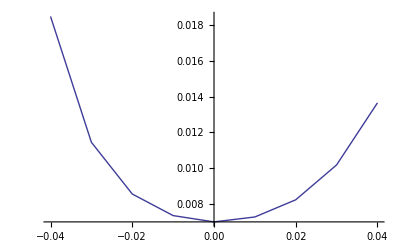

```mathematica
x=-0.05;
m=0.05;
Clear[a]
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.04,0.04,0.01}],Joined->True]
```

# Linear arrangement XMA

## life-cycle

Haploid selection

```mathematica
Subscript[wbarHap, sex_]:=Subscript[wbarHap, sex]=ParallelSum[Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex],{x,{X,Y}},{y,{A,a}},{z,{M,m}}];
Subscript[fHapSel, x_,y_,z_,sex_]:=Subscript[wHap, y,sex] Subscript[fHap, x,y,z,sex]/Subscript[wbarHap, sex]
```

Random mating

```mathematica
Subscript[fDip, xM_,yM_,zM_,xP_,yP_,zP_]:=Subscript[fDip, xM,yM,zM,xP,yP,zP]=Subscript[fHapSel, xM,yM,zM,female] Subscript[fHapSel, xP,yP,zP,male]
```

Sex determination

```mathematica
Subscript[fDipSex, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]=Subscript[fDip, xM,yM,zM,xP,yP,zP] Subscript[psex, zM,xP,zP,sex]
```

where a diploid must become male or female

```mathematica
sumsex=Subscript[psex, zM_,xP_,zP_,male]->1-Subscript[psex, zM,xP,zP,female];
```

We assume the invasion of a dominant modifier into an XY system

```mathematica
invXY={
Subscript[psex, M,Y,M,female]->0,(*always male if ESD wildtype and have Y*)
Subscript[psex, M,X,M,female]->1,(*always female ESD wildtype and have X from father*)
Subscript[psex, m,xP_,zP_,female]->k,(*female with probability k if mutation at the ESD*)
Subscript[psex, zM_,xP_,m,female]->k
};
```

Diploid selection

```mathematica
Subscript[wbarDip, sex_]:=Subscript[wbarDip, sex]=ParallelSum[Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}];
Subscript[fDipSel, xM_,yM_,zM_,xP_,yP_,zP_,sex_]:=Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex]=Subscript[wDip, yM,yP,sex] Subscript[fDipSex, xM,yM,zM,xP,yP,zP,sex]/Subscript[wbarDip, sex]
```

Meiosis

```mathematica
Subscript[fHapNext, x_,y_,z_,sex_]:=Subscript[fHapNext, x,y,z,sex]=ParallelSum[Subscript[fDipSel, xM,yM,zM,xP,yP,zP,sex] Subscript[pseg, xM,yM,zM,xP,yP,zP,sex,x,y,z],{xM,{X,Y}},{yM,{A,a}},{zM,{M,m}},{xP,{X,Y}},{yP,{A,a}},{zP,{M,m}}]
```

Segregation rules with female and male-specific meiotic drive (individuals of sex i who are heterozygous at the viablilty locus produce α_i% A haplotypes and 1-α_i% a haplotypes before selection)

```mathematica
pseg0={
(*triple homozygote*)
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z1_,sex_,x1_,y1_,z1_]->1
};
pseg1={
(*single heterozygotes*)
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z1_,sex_,x2_,y1_,z1_]->1/2,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,A,z1_]->Subscript[α, male] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male]),
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,A,z1_,x1_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,A,z1_]->Subscript[α, female] ,
Subscript[pseg, x1_,a,z1_,x1_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]),
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z1_]->1/2,
Subscript[pseg, x1_,y1_,z1_,x1_,y1_,z2_,sex_,x1_,y1_,z2_]->1/2
};
pseg2={
(*double heterozygotes*)
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,A,z1_]->Subscript[α, male]((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x2_,A,z1_]->Subscript[α, male] (χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])(χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,A,z1_]->Subscript[α, male]  (χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,a,z1_]->(1-Subscript[α, male])(χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x2_,A,z1_]->Subscript[α, male] ((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,male,x1_,a,z1_]->(1-Subscript[α, male])((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z1_]->Subscript[α, male] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,A,z2_]->Subscript[α, male] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,A,z1_]->Subscript[α, female]((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,a,z1_]->(1-Subscript[α, female])((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x2_,A,z1_]->Subscript[α, female] (χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,A,z1_,x2_,a,z1_,female,x1_,a,z1_]->(1-Subscript[α, female])(χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])(1-R),
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] R,
Subscript[pseg, x1_,A,z1_,x1_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,A,z1_]->Subscript[α, female]  (χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,a,z1_]->(1-Subscript[α, female]) (χ(1-R)+(1-χ)R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x2_,A,z1_]->Subscript[α, female] ((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,a,z1_,x2_,A,z1_,female,x1_,a,z1_]->(1-Subscript[α, female]) ((1-χ)(1-R)+χ R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])R,
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] (1-R),
Subscript[pseg, x1_,a,z1_,x1_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-R),
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z1_]->(1-χ)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z2_]->(1-χ)/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x2_,y1_,z1_]->χ/2,
Subscript[pseg, x1_,y1_,z1_,x2_,y1_,z2_,sex_,x1_,y1_,z2_]->χ/2
};
pseg3={
(*triple heterozygote*)
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z1_]->Subscript[α, male](1-χ)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-χ)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z1_]->Subscript[α, male] χ(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])χ(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-χ) R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-χ) R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x1_,A,z2_]->Subscript[α, male] χ R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,male,x2_,a,z1_]->(1-Subscript[α, male])χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z1_]->Subscript[α, male](1-χ) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z2_]->(1-Subscript[α, male])(1-χ) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z1_]->Subscript[α, male] χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z2_]->(1-Subscript[α, male])χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,A,z2_]->Subscript[α, male] (1-χ)(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,a,z1_]->(1-Subscript[α, male]) (1-χ)(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x1_,A,z2_]->Subscript[α, male]  χ(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,male,x2_,a,z1_]->(1-Subscript[α, male]) χ(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z1_]->Subscript[α, female](1-χ)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-χ)(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z1_]->Subscript[α, female] χ(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])χ(1-R),
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-χ) R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,a,z1_]->(1-Subscript[α, female]) (1-χ) R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x1_,A,z2_]->Subscript[α, female] χ R,
Subscript[pseg, x1_,A,z1_,x2_,a,z2_,female,x2_,a,z1_]->(1-Subscript[α, female])χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z1_]->Subscript[α, female] (1-χ) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z2_]->(1-Subscript[α, female])(1-χ) R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z1_]->Subscript[α, female] χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z2_]->(1-Subscript[α, female])χ R,
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,A,z2_]->Subscript[α, female] (1-χ)(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,a,z1_]->(1-Subscript[α, female])(1-χ)(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x1_,A,z2_]->Subscript[α, female] χ(1-R),
Subscript[pseg, x1_,a,z1_,x2_,A,z2_,female,x2_,a,z1_]->(1-Subscript[α, female]) χ(1-R)
};
pseg4=Subscript[pseg, x1_,y1_,z1_,x2_,y2_,z2_,sex_,x_,y_,z_]->0;
```

## find resident equilibrium

```mathematica
subequil={
Subscript[fHap, X,A,M,female]->pXf,
Subscript[fHap, X,a,M,female]->1-pXf,
Subscript[fHap, X,A,M,male]->pXm *(1-freqYm),
Subscript[fHap, X,a,M,male]->(1-pXm)(1-freqYm),
Subscript[fHap, Y,A,M,male]->pYm freqYm,
Subscript[fHap, Y,a,M,male]->(1-pYm)freqYm,
Subscript[fHap, x_,y_,m,sex_]->0,
Subscript[fHap, Y,y_,M,female]->0
};
```

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
Subscript[fHapNext, X,A,M,female]-Subscript[fHap, X,A,M,female],
Subscript[fHapNext, X,A,M,male]-Subscript[fHap, X,A,M,male],
Subscript[fHapNext, Y,A,M,male]-Subscript[fHap, Y,A,M,male],
(Subscript[fHapNext, Y,A,M,male]+Subscript[fHapNext, Y,a,M,male])-(Subscript[fHap, Y,A,M,male]+Subscript[fHap, Y,a,M,male])
}/.subequil/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4;
```

Shorten expressions up with some substitutions and copy and paste into function to find equibria

```mathematica
varsub={Subscript[wDip, A,A,female]->FAA,Subscript[wDip, A,a,female]->FAa,Subscript[wDip, a,A,female]->FAa,Subscript[wDip, a,a,female]->Faa,Subscript[wDip, A,A,male]->MAA,Subscript[wDip, A,a,male]->MAa,Subscript[wDip, a,A,male]->MAa,Subscript[wDip, a,a,male]->Maa,Subscript[wHap, A,male]->MA,Subscript[wHap, a,male]->Ma,Subscript[wHap, A,female]->FA,Subscript[wHap, a,female]->Fa,Subscript[α, male]->MdA,Subscript[α, female]->FdA};
differenceEqs/.varsub//Simplify
```

{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)-MA MAa pYm ((-1+freqYm) pXm+MdA (R+χ-2 R χ)))+FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm-2 Ma MAa (-1+pYm) ((-1+freqYm) pXm+MdA (1-χ+R (-1+2 χ)))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)+2 Ma MAa MdA (-1+pYm) (-R-χ+2 R χ))-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)+MA MAa MdA (1-χ+R (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ)))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}

```mathematica
Clear[equilXMA]
equilXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)-MA MAa pYm ((-1+freqYm) pXm+MdA (R+χ-2 R χ)))+FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm-2 Ma MAa (-1+pYm) ((-1+freqYm) pXm+MdA (1-χ+R (-1+2 χ)))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)+2 Ma MAa MdA (-1+pYm) (-R-χ+2 R χ))-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)+MA MAa MdA (1-χ+R (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ)))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXMA]
sieveXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXMA[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

## characteristic polynomial

The characteristic polynomial for invasion into XY is

```mathematica
(*eqsmut=ParallelTable[Subscript[fHapNext, x,y,m,sex],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}]/.sumsex/.invXY/.pseg0/.pseg1/.pseg2/.pseg3/.pseg4//Flatten;
jac=Transpose[Flatten[ParallelTable[D[eqsmut,Subscript[fHap, x,y,m,sex]],{sex,{male,female}},{y,{A,a}},{x,{X,Y}}],2]]/.subequil//Factor;
detjac=Det[jac-IdentityMatrix[8]*λ];*)
```

And for a neo-W this reduces to

```mathematica
(*detjac/.k->1/.varsub*)
```

```mathematica
detjack1=(λ^2 (-2 FA FAa (-1+FdA) freqYm Ma (-1+pYm) R χ (-2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ))-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ)+16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))+2 FA FAa (-1+FdA) Ma R (-1+pXm-freqYm pXm+freqYm pYm+χ-freqYm χ-pXm χ+freqYm pXm χ) (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (16 Fa^2 FAa^2 FdA^2 (-1+freqYm) freqYm^3 MA^2 pXm pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 χ^2-16 Fa^2 FAa^2 FdA^2 freqYm^2 MA^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R^2 λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ)+16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)-2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))-(Fa freqYm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pYm-2 FAa MA pYm+2 FAa FdA MA pYm+2 FAa MA pYm R-2 FAa FdA MA pYm R) χ (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ)+16 Fa FAa FdA (-1+freqYm)^2 freqYm^2 MA pXm (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pXm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (pXm-freqYm pXm+freqYm pYm-pXm χ+freqYm pXm χ) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))-(Fa (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Faa Ma+Faa Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa MA pXm R-2 FAa FdA MA pXm R) χ (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)))/(Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm)+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ+(Fa (-Faa Ma+Faa Ma pXm-Faa freqYm Ma pXm-2 FAa MA pXm+2 FAa FdA MA pXm+2 FAa freqYm MA pXm-2 FAa FdA freqYm MA pXm+Faa freqYm Ma pYm-2 FAa freqYm MA pYm+2 FAa FdA freqYm MA pYm+2 FAa MA pXm R-2 FAa FdA MA pXm R-2 FAa freqYm MA pXm R+2 FAa FdA freqYm MA pXm R+2 FAa freqYm MA pYm R-2 FAa FdA freqYm MA pYm R+Faa Ma χ-Faa freqYm Ma χ-Faa Ma pXm χ+Faa freqYm Ma pXm χ+2 FAa MA pXm χ-2 FAa FdA MA pXm χ-2 FAa freqYm MA pXm χ+2 FAa FdA freqYm MA pXm χ-2 FAa MA pXm R χ+2 FAa FdA MA pXm R χ+2 FAa freqYm MA pXm R χ-2 FAa FdA freqYm MA pXm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (-2 FA FAa (-1+FdA) Ma R (1-pXm+freqYm pXm-freqYm pYm-freqYm χ+freqYm pYm χ) (-8 Fa FA FAa FdA (-1+freqYm) freqYm^3 MA pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) λ^2 χ^2+16 Fa FAa FdA (-1+freqYm) freqYm^2 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ) (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 FA FAa (-1+FdA) (-1+freqYm) Ma (-1+pXm) R χ (8 Fa FA FAa FdA freqYm^3 MA (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ (-pXm+freqYm pXm-freqYm pYm+freqYm pYm χ)+16 Fa FAa FdA (-1+freqYm) freqYm^3 MA (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) pYm (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 R λ^2 χ (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))))+2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm) (-λ-(Fa (Faa Ma-Faa Ma pXm+Faa freqYm Ma pXm+2 FAa MA pXm-2 FAa FdA MA pXm-2 FAa freqYm MA pXm+2 FAa FdA freqYm MA pXm-Faa freqYm Ma pYm+2 FAa freqYm MA pYm-2 FAa FdA freqYm MA pYm-2 FAa MA pXm R+2 FAa FdA MA pXm R+2 FAa freqYm MA pXm R-2 FAa FdA freqYm MA pXm R-2 FAa freqYm MA pYm R+2 FAa FdA freqYm MA pYm R-Faa freqYm Ma χ+Faa freqYm Ma pYm χ-2 FAa freqYm MA pYm χ+2 FAa FdA freqYm MA pYm χ+2 FAa freqYm MA pYm R χ-2 FAa FdA freqYm MA pYm R χ))/(2 (-1+freqYm) (Fa Faa Ma-Fa Faa Ma pXf+FA FAa Ma pXf-Fa Faa Ma pXm+Fa FAa MA pXm+Fa Faa Ma pXf pXm-FA FAa Ma pXf pXm-Fa FAa MA pXf pXm+FA FAA MA pXf pXm))) (4 FA^2 (-1+freqYm) freqYm^3 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 (2 FAa FdA Ma-2 FAa FdA Ma pXm+FAA MA pXm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R) (2 FAa FdA Ma-2 FAa FdA Ma pYm+FAA MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pYm R) λ^2 χ^2+16 (-1+freqYm)^2 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^2 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2 λ^2 (-λ+(FA (2 FAa FdA Ma-2 FAa FdA Ma pXm+2 FAa FdA freqYm Ma pXm+FAA MA pXm-FAA freqYm MA pXm-2 FAa FdA freqYm Ma pYm+FAA freqYm MA pYm-2 FAa FdA Ma R+2 FAa FdA Ma pXm R-2 FAa FdA freqYm Ma pXm R+2 FAa FdA freqYm Ma pYm R-2 FAa FdA Ma χ+2 FAa FdA freqYm Ma χ+2 FAa FdA Ma pXm χ-2 FAa FdA freqYm Ma pXm χ-FAA MA pXm χ+FAA freqYm MA pXm χ+2 FAa FdA Ma R χ-2 FAa FdA freqYm Ma R χ-2 FAa FdA Ma pXm R χ+2 FAa FdA freqYm Ma pXm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm))) (-λ-(FA (-2 FAa FdA Ma+2 FAa FdA Ma pXm-2 FAa FdA freqYm Ma pXm-FAA MA pXm+FAA freqYm MA pXm+2 FAa FdA freqYm Ma pYm-FAA freqYm MA pYm+2 FAa FdA Ma R-2 FAa FdA Ma pXm R+2 FAa FdA freqYm Ma pXm R-2 FAa FdA freqYm Ma pYm R+2 FAa FdA freqYm Ma χ-2 FAa FdA freqYm Ma pYm χ+FAA freqYm MA pYm χ-2 FAa FdA freqYm Ma R χ+2 FAa FdA freqYm Ma pYm R χ))/(2 (-1+freqYm) (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)))))))/(64 (-1+freqYm)^4 freqYm^2 (-Fa Faa Ma+Fa Faa Ma pXf-FA FAa Ma pXf+Fa Faa Ma pXm-Fa FAa MA pXm-Fa Faa Ma pXf pXm+FA FAa Ma pXf pXm+Fa FAa MA pXf pXm-FA FAA MA pXf pXm)^4 (-Fa Ma Maa+Fa Ma Maa pXf-FA Ma MAa pXf+Fa Ma Maa pYm-Fa MA MAa pYm-Fa Ma Maa pXf pYm+FA Ma MAa pXf pYm+Fa MA MAa pXf pYm-FA MA MAA pXf pYm)^2);
```

If there is no meiotic drive this reduces further and can be factored

```mathematica
(*detjack1/.MdA->1/2/.FdA->1/2/.freqYm->1/2//Factor*)
```

```mathematica
detjack1nodrive=(λ^4 (4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-4 FAa^2 Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+2 FAa^2 Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-4 FAa^2 Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+4 FAa^2 Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+2 FAa^2 Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R-4 Faa^2 Ma^2 λ-4 Faa FAa Ma^2 λ+4 Faa^2 Ma^2 pXf λ-4 FAa^2 Ma^2 pXf λ+6 Faa^2 Ma^2 pXm λ+6 Faa FAa Ma^2 pXm λ-6 Faa FAa Ma MA pXm λ-4 FAa^2 Ma MA pXm λ-2 Faa FAA Ma MA pXm λ-6 Faa^2 Ma^2 pXf pXm λ+6 FAa^2 Ma^2 pXf pXm λ+6 Faa FAa Ma MA pXf pXm λ+2 FAa^2 Ma MA pXf pXm λ-2 Faa FAA Ma MA pXf pXm λ-6 FAa FAA Ma MA pXf pXm λ-2 Faa^2 Ma^2 pXm^2 λ-2 Faa FAa Ma^2 pXm^2 λ+4 Faa FAa Ma MA pXm^2 λ+2 FAa^2 Ma MA pXm^2 λ+2 Faa FAA Ma MA pXm^2 λ-2 FAa^2 MA^2 pXm^2 λ-2 FAa FAA MA^2 pXm^2 λ+2 Faa^2 Ma^2 pXf pXm^2 λ-2 FAa^2 Ma^2 pXf pXm^2 λ-4 Faa FAa Ma MA pXf pXm^2 λ+4 FAa FAA Ma MA pXf pXm^2 λ+2 FAa^2 MA^2 pXf pXm^2 λ-2 FAA^2 MA^2 pXf pXm^2 λ+2 Faa^2 Ma^2 pYm λ+2 Faa FAa Ma^2 pYm λ-2 Faa FAa Ma MA pYm λ-2 Faa FAA Ma MA pYm λ-2 Faa^2 Ma^2 pXf pYm λ+2 FAa^2 Ma^2 pXf pYm λ+2 Faa FAa Ma MA pXf pYm λ-2 FAa^2 Ma MA pXf pYm λ+2 Faa FAA Ma MA pXf pYm λ-2 FAa FAA Ma MA pXf pYm λ-2 Faa^2 Ma^2 pXm pYm λ-2 Faa FAa Ma^2 pXm pYm λ+4 Faa FAa Ma MA pXm pYm λ+2 FAa^2 Ma MA pXm pYm λ+2 Faa FAA Ma MA pXm pYm λ-2 FAa^2 MA^2 pXm pYm λ-2 FAa FAA MA^2 pXm pYm λ+2 Faa^2 Ma^2 pXf pXm pYm λ-2 FAa^2 Ma^2 pXf pXm pYm λ-4 Faa FAa Ma MA pXf pXm pYm λ+4 FAa FAA Ma MA pXf pXm pYm λ+2 FAa^2 MA^2 pXf pXm pYm λ-2 FAA^2 MA^2 pXf pXm pYm λ+4 Faa FAa Ma^2 R λ-4 Faa FAa Ma^2 pXf R λ+4 FAa^2 Ma^2 pXf R λ-6 Faa FAa Ma^2 pXm R λ+2 Faa FAa Ma MA pXm R λ+4 FAa^2 Ma MA pXm R λ+6 Faa FAa Ma^2 pXf pXm R λ-6 FAa^2 Ma^2 pXf pXm R λ-2 Faa FAa Ma MA pXf pXm R λ-2 FAa^2 Ma MA pXf pXm R λ+4 FAa FAA Ma MA pXf pXm R λ+2 Faa FAa Ma^2 pXm^2 R λ-2 Faa FAa Ma MA pXm^2 R λ-2 FAa^2 Ma MA pXm^2 R λ+2 FAa^2 MA^2 pXm^2 R λ-2 Faa FAa Ma^2 pXf pXm^2 R λ+2 FAa^2 Ma^2 pXf pXm^2 R λ+2 Faa FAa Ma MA pXf pXm^2 R λ-2 FAa FAA Ma MA pXf pXm^2 R λ-2 FAa^2 MA^2 pXf pXm^2 R λ+2 FAa FAA MA^2 pXf pXm^2 R λ-2 Faa FAa Ma^2 pYm R λ+2 Faa FAa Ma MA pYm R λ+2 Faa FAa Ma^2 pXf pYm R λ-2 FAa^2 Ma^2 pXf pYm R λ-2 Faa FAa Ma MA pXf pYm R λ+2 FAa^2 Ma MA pXf pYm R λ+2 Faa FAa Ma^2 pXm pYm R λ-2 Faa FAa Ma MA pXm pYm R λ-2 FAa^2 Ma MA pXm pYm R λ+2 FAa^2 MA^2 pXm pYm R λ-2 Faa FAa Ma^2 pXf pXm pYm R λ+2 FAa^2 Ma^2 pXf pXm pYm R λ+2 Faa FAa Ma MA pXf pXm pYm R λ-2 FAa FAA Ma MA pXf pXm pYm R λ-2 FAa^2 MA^2 pXf pXm pYm R λ+2 FAa FAA MA^2 pXf pXm pYm R λ+4 Faa^2 Ma^2 λ^2-8 Faa^2 Ma^2 pXf λ^2+8 Faa FAa Ma^2 pXf λ^2+4 Faa^2 Ma^2 pXf^2 λ^2-8 Faa FAa Ma^2 pXf^2 λ^2+4 FAa^2 Ma^2 pXf^2 λ^2-8 Faa^2 Ma^2 pXm λ^2+8 Faa FAa Ma MA pXm λ^2+16 Faa^2 Ma^2 pXf pXm λ^2-16 Faa FAa Ma^2 pXf pXm λ^2-16 Faa FAa Ma MA pXf pXm λ^2+8 FAa^2 Ma MA pXf pXm λ^2+8 Faa FAA Ma MA pXf pXm λ^2-8 Faa^2 Ma^2 pXf^2 pXm λ^2+16 Faa FAa Ma^2 pXf^2 pXm λ^2-8 FAa^2 Ma^2 pXf^2 pXm λ^2+8 Faa FAa Ma MA pXf^2 pXm λ^2-8 FAa^2 Ma MA pXf^2 pXm λ^2-8 Faa FAA Ma MA pXf^2 pXm λ^2+8 FAa FAA Ma MA pXf^2 pXm λ^2+4 Faa^2 Ma^2 pXm^2 λ^2-8 Faa FAa Ma MA pXm^2 λ^2+4 FAa^2 MA^2 pXm^2 λ^2-8 Faa^2 Ma^2 pXf pXm^2 λ^2+8 Faa FAa Ma^2 pXf pXm^2 λ^2+16 Faa FAa Ma MA pXf pXm^2 λ^2-8 FAa^2 Ma MA pXf pXm^2 λ^2-8 Faa FAA Ma MA pXf pXm^2 λ^2-8 FAa^2 MA^2 pXf pXm^2 λ^2+8 FAa FAA MA^2 pXf pXm^2 λ^2+4 Faa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Faa FAa Ma^2 pXf^2 pXm^2 λ^2+4 FAa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Faa FAa Ma MA pXf^2 pXm^2 λ^2+8 FAa^2 Ma MA pXf^2 pXm^2 λ^2+8 Faa FAA Ma MA pXf^2 pXm^2 λ^2-8 FAa FAA Ma MA pXf^2 pXm^2 λ^2+4 FAa^2 MA^2 pXf^2 pXm^2 λ^2-8 FAa FAA MA^2 pXf^2 pXm^2 λ^2+4 FAA^2 MA^2 pXf^2 pXm^2 λ^2) (4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-4 FAa^2 Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+2 FAa^2 Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-4 FAa^2 Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+4 FAa^2 Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+2 FAa^2 Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R-4 Faa^2 Ma^2 λ-4 Faa FAa Ma^2 λ+4 Faa^2 Ma^2 pXf λ-4 FAa^2 Ma^2 pXf λ+6 Faa^2 Ma^2 pXm λ+6 Faa FAa Ma^2 pXm λ-6 Faa FAa Ma MA pXm λ-4 FAa^2 Ma MA pXm λ-2 Faa FAA Ma MA pXm λ-6 Faa^2 Ma^2 pXf pXm λ+6 FAa^2 Ma^2 pXf pXm λ+6 Faa FAa Ma MA pXf pXm λ+2 FAa^2 Ma MA pXf pXm λ-2 Faa FAA Ma MA pXf pXm λ-6 FAa FAA Ma MA pXf pXm λ-2 Faa^2 Ma^2 pXm^2 λ-2 Faa FAa Ma^2 pXm^2 λ+4 Faa FAa Ma MA pXm^2 λ+2 FAa^2 Ma MA pXm^2 λ+2 Faa FAA Ma MA pXm^2 λ-2 FAa^2 MA^2 pXm^2 λ-2 FAa FAA MA^2 pXm^2 λ+2 Faa^2 Ma^2 pXf pXm^2 λ-2 FAa^2 Ma^2 pXf pXm^2 λ-4 Faa FAa Ma MA pXf pXm^2 λ+4 FAa FAA Ma MA pXf pXm^2 λ+2 FAa^2 MA^2 pXf pXm^2 λ-2 FAA^2 MA^2 pXf pXm^2 λ+2 Faa^2 Ma^2 pYm λ+2 Faa FAa Ma^2 pYm λ-2 Faa FAa Ma MA pYm λ-2 Faa FAA Ma MA pYm λ-2 Faa^2 Ma^2 pXf pYm λ+2 FAa^2 Ma^2 pXf pYm λ+2 Faa FAa Ma MA pXf pYm λ-2 FAa^2 Ma MA pXf pYm λ+2 Faa FAA Ma MA pXf pYm λ-2 FAa FAA Ma MA pXf pYm λ-2 Faa^2 Ma^2 pXm pYm λ-2 Faa FAa Ma^2 pXm pYm λ+4 Faa FAa Ma MA pXm pYm λ+2 FAa^2 Ma MA pXm pYm λ+2 Faa FAA Ma MA pXm pYm λ-2 FAa^2 MA^2 pXm pYm λ-2 FAa FAA MA^2 pXm pYm λ+2 Faa^2 Ma^2 pXf pXm pYm λ-2 FAa^2 Ma^2 pXf pXm pYm λ-4 Faa FAa Ma MA pXf pXm pYm λ+4 FAa FAA Ma MA pXf pXm pYm λ+2 FAa^2 MA^2 pXf pXm pYm λ-2 FAA^2 MA^2 pXf pXm pYm λ+4 Faa FAa Ma^2 R λ-4 Faa FAa Ma^2 pXf R λ+4 FAa^2 Ma^2 pXf R λ-6 Faa FAa Ma^2 pXm R λ+2 Faa FAa Ma MA pXm R λ+4 FAa^2 Ma MA pXm R λ+6 Faa FAa Ma^2 pXf pXm R λ-6 FAa^2 Ma^2 pXf pXm R λ-2 Faa FAa Ma MA pXf pXm R λ-2 FAa^2 Ma MA pXf pXm R λ+4 FAa FAA Ma MA pXf pXm R λ+2 Faa FAa Ma^2 pXm^2 R λ-2 Faa FAa Ma MA pXm^2 R λ-2 FAa^2 Ma MA pXm^2 R λ+2 FAa^2 MA^2 pXm^2 R λ-2 Faa FAa Ma^2 pXf pXm^2 R λ+2 FAa^2 Ma^2 pXf pXm^2 R λ+2 Faa FAa Ma MA pXf pXm^2 R λ-2 FAa FAA Ma MA pXf pXm^2 R λ-2 FAa^2 MA^2 pXf pXm^2 R λ+2 FAa FAA MA^2 pXf pXm^2 R λ-2 Faa FAa Ma^2 pYm R λ+2 Faa FAa Ma MA pYm R λ+2 Faa FAa Ma^2 pXf pYm R λ-2 FAa^2 Ma^2 pXf pYm R λ-2 Faa FAa Ma MA pXf pYm R λ+2 FAa^2 Ma MA pXf pYm R λ+2 Faa FAa Ma^2 pXm pYm R λ-2 Faa FAa Ma MA pXm pYm R λ-2 FAa^2 Ma MA pXm pYm R λ+2 FAa^2 MA^2 pXm pYm R λ-2 Faa FAa Ma^2 pXf pXm pYm R λ+2 FAa^2 Ma^2 pXf pXm pYm R λ+2 Faa FAa Ma MA pXf pXm pYm R λ-2 FAa FAA Ma MA pXf pXm pYm R λ-2 FAa^2 MA^2 pXf pXm pYm R λ+2 FAa FAA MA^2 pXf pXm pYm R λ+4 Faa^2 Ma^2 λ^2-8 Faa^2 Ma^2 pXf λ^2+8 Faa FAa Ma^2 pXf λ^2+4 Faa^2 Ma^2 pXf^2 λ^2-8 Faa FAa Ma^2 pXf^2 λ^2+4 FAa^2 Ma^2 pXf^2 λ^2-8 Faa^2 Ma^2 pXm λ^2+8 Faa FAa Ma MA pXm λ^2+16 Faa^2 Ma^2 pXf pXm λ^2-16 Faa FAa Ma^2 pXf pXm λ^2-16 Faa FAa Ma MA pXf pXm λ^2+8 FAa^2 Ma MA pXf pXm λ^2+8 Faa FAA Ma MA pXf pXm λ^2-8 Faa^2 Ma^2 pXf^2 pXm λ^2+16 Faa FAa Ma^2 pXf^2 pXm λ^2-8 FAa^2 Ma^2 pXf^2 pXm λ^2+8 Faa FAa Ma MA pXf^2 pXm λ^2-8 FAa^2 Ma MA pXf^2 pXm λ^2-8 Faa FAA Ma MA pXf^2 pXm λ^2+8 FAa FAA Ma MA pXf^2 pXm λ^2+4 Faa^2 Ma^2 pXm^2 λ^2-8 Faa FAa Ma MA pXm^2 λ^2+4 FAa^2 MA^2 pXm^2 λ^2-8 Faa^2 Ma^2 pXf pXm^2 λ^2+8 Faa FAa Ma^2 pXf pXm^2 λ^2+16 Faa FAa Ma MA pXf pXm^2 λ^2-8 FAa^2 Ma MA pXf pXm^2 λ^2-8 Faa FAA Ma MA pXf pXm^2 λ^2-8 FAa^2 MA^2 pXf pXm^2 λ^2+8 FAa FAA MA^2 pXf pXm^2 λ^2+4 Faa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Faa FAa Ma^2 pXf^2 pXm^2 λ^2+4 FAa^2 Ma^2 pXf^2 pXm^2 λ^2-8 Faa FAa Ma MA pXf^2 pXm^2 λ^2+8 FAa^2 Ma MA pXf^2 pXm^2 λ^2+8 Faa FAA Ma MA pXf^2 pXm^2 λ^2-8 FAa FAA Ma MA pXf^2 pXm^2 λ^2+4 FAa^2 MA^2 pXf^2 pXm^2 λ^2-8 FAa FAA MA^2 pXf^2 pXm^2 λ^2+4 FAA^2 MA^2 pXf^2 pXm^2 λ^2-8 Faa FAa Ma^2 χ+8 Faa FAa Ma^2 pXm χ-4 FAa^2 Ma MA pXm χ-4 Faa FAA Ma MA pXm χ-2 Faa FAa Ma^2 pXm^2 χ+2 FAa^2 Ma MA pXm^2 χ+2 Faa FAA Ma MA pXm^2 χ-2 FAa FAA MA^2 pXm^2 χ+8 Faa FAa Ma^2 pYm χ-4 FAa^2 Ma MA pYm χ-4 Faa FAA Ma MA pYm χ-4 Faa FAa Ma^2 pXm pYm χ+4 FAa^2 Ma MA pXm pYm χ+4 Faa FAA Ma MA pXm pYm χ-4 FAa FAA MA^2 pXm pYm χ-2 Faa FAa Ma^2 pYm^2 χ+2 FAa^2 Ma MA pYm^2 χ+2 Faa FAA Ma MA pYm^2 χ-2 FAa FAA MA^2 pYm^2 χ+8 Faa FAa Ma^2 R χ-8 Faa FAa Ma^2 pXm R χ+8 FAa^2 Ma MA pXm R χ+2 Faa FAa Ma^2 pXm^2 R χ-4 FAa^2 Ma MA pXm^2 R χ+2 FAa FAA MA^2 pXm^2 R χ-8 Faa FAa Ma^2 pYm R χ+8 FAa^2 Ma MA pYm R χ+4 Faa FAa Ma^2 pXm pYm R χ-8 FAa^2 Ma MA pXm pYm R χ+4 FAa FAA MA^2 pXm pYm R χ+2 Faa FAa Ma^2 pYm^2 R χ-4 FAa^2 Ma MA pYm^2 R χ+2 FAa FAA MA^2 pYm^2 R χ+4 Faa^2 Ma^2 λ χ+4 Faa FAa Ma^2 λ χ-4 Faa^2 Ma^2 pXf λ χ+4 FAa^2 Ma^2 pXf λ χ-6 Faa^2 Ma^2 pXm λ χ-6 Faa FAa Ma^2 pXm λ χ+6 Faa FAa Ma MA pXm λ χ+4 FAa^2 Ma MA pXm λ χ+2 Faa FAA Ma MA pXm λ χ+6 Faa^2 Ma^2 pXf pXm λ χ-6 FAa^2 Ma^2 pXf pXm λ χ-6 Faa FAa Ma MA pXf pXm λ χ-2 FAa^2 Ma MA pXf pXm λ χ+2 Faa FAA Ma MA pXf pXm λ χ+6 FAa FAA Ma MA pXf pXm λ χ+2 Faa^2 Ma^2 pXm^2 λ χ+2 Faa FAa Ma^2 pXm^2 λ χ-4 Faa FAa Ma MA pXm^2 λ χ-2 FAa^2 Ma MA pXm^2 λ χ-2 Faa FAA Ma MA pXm^2 λ χ+2 FAa^2 MA^2 pXm^2 λ χ+2 FAa FAA MA^2 pXm^2 λ χ-2 Faa^2 Ma^2 pXf pXm^2 λ χ+2 FAa^2 Ma^2 pXf pXm^2 λ χ+4 Faa FAa Ma MA pXf pXm^2 λ χ-4 FAa FAA Ma MA pXf pXm^2 λ χ-2 FAa^2 MA^2 pXf pXm^2 λ χ+2 FAA^2 MA^2 pXf pXm^2 λ χ-2 Faa^2 Ma^2 pYm λ χ-2 Faa FAa Ma^2 pYm λ χ+2 Faa FAa Ma MA pYm λ χ+2 Faa FAA Ma MA pYm λ χ+2 Faa^2 Ma^2 pXf pYm λ χ-2 FAa^2 Ma^2 pXf pYm λ χ-2 Faa FAa Ma MA pXf pYm λ χ+2 FAa^2 Ma MA pXf pYm λ χ-2 Faa FAA Ma MA pXf pYm λ χ+2 FAa FAA Ma MA pXf pYm λ χ+2 Faa^2 Ma^2 pXm pYm λ χ+2 Faa FAa Ma^2 pXm pYm λ χ-4 Faa FAa Ma MA pXm pYm λ χ-2 FAa^2 Ma MA pXm pYm λ χ-2 Faa FAA Ma MA pXm pYm λ χ+2 FAa^2 MA^2 pXm pYm λ χ+2 FAa FAA MA^2 pXm pYm λ χ-2 Faa^2 Ma^2 pXf pXm pYm λ χ+2 FAa^2 Ma^2 pXf pXm pYm λ χ+4 Faa FAa Ma MA pXf pXm pYm λ χ-4 FAa FAA Ma MA pXf pXm pYm λ χ-2 FAa^2 MA^2 pXf pXm pYm λ χ+2 FAA^2 MA^2 pXf pXm pYm λ χ-4 Faa FAa Ma^2 R λ χ+4 Faa FAa Ma^2 pXf R λ χ-4 FAa^2 Ma^2 pXf R λ χ+6 Faa FAa Ma^2 pXm R λ χ-2 Faa FAa Ma MA pXm R λ χ-4 FAa^2 Ma MA pXm R λ χ-6 Faa FAa Ma^2 pXf pXm R λ χ+6 FAa^2 Ma^2 pXf pXm R λ χ+2 Faa FAa Ma MA pXf pXm R λ χ+2 FAa^2 Ma MA pXf pXm R λ χ-4 FAa FAA Ma MA pXf pXm R λ χ-2 Faa FAa Ma^2 pXm^2 R λ χ+2 Faa FAa Ma MA pXm^2 R λ χ+2 FAa^2 Ma MA pXm^2 R λ χ-2 FAa^2 MA^2 pXm^2 R λ χ+2 Faa FAa Ma^2 pXf pXm^2 R λ χ-2 FAa^2 Ma^2 pXf pXm^2 R λ χ-2 Faa FAa Ma MA pXf pXm^2 R λ χ+2 FAa FAA Ma MA pXf pXm^2 R λ χ+2 FAa^2 MA^2 pXf pXm^2 R λ χ-2 FAa FAA MA^2 pXf pXm^2 R λ χ+2 Faa FAa Ma^2 pYm R λ χ-2 Faa FAa Ma MA pYm R λ χ-2 Faa FAa Ma^2 pXf pYm R λ χ+2 FAa^2 Ma^2 pXf pYm R λ χ+2 Faa FAa Ma MA pXf pYm R λ χ-2 FAa^2 Ma MA pXf pYm R λ χ-2 Faa FAa Ma^2 pXm pYm R λ χ+2 Faa FAa Ma MA pXm pYm R λ χ+2 FAa^2 Ma MA pXm pYm R λ χ-2 FAa^2 MA^2 pXm pYm R λ χ+2 Faa FAa Ma^2 pXf pXm pYm R λ χ-2 FAa^2 Ma^2 pXf pXm pYm R λ χ-2 Faa FAa Ma MA pXf pXm pYm R λ χ+2 FAa FAA Ma MA pXf pXm pYm R λ χ+2 FAa^2 MA^2 pXf pXm pYm R λ χ-2 FAa FAA MA^2 pXf pXm pYm R λ χ+4 Faa FAa Ma^2 χ^2-4 Faa FAa Ma^2 pXm χ^2+2 FAa^2 Ma MA pXm χ^2+2 Faa FAA Ma MA pXm χ^2+Faa FAa Ma^2 pXm^2 χ^2-FAa^2 Ma MA pXm^2 χ^2-Faa FAA Ma MA pXm^2 χ^2+FAa FAA MA^2 pXm^2 χ^2-4 Faa FAa Ma^2 pYm χ^2+2 FAa^2 Ma MA pYm χ^2+2 Faa FAA Ma MA pYm χ^2+2 Faa FAa Ma^2 pXm pYm χ^2-2 FAa^2 Ma MA pXm pYm χ^2-2 Faa FAA Ma MA pXm pYm χ^2+2 FAa FAA MA^2 pXm pYm χ^2+Faa FAa Ma^2 pYm^2 χ^2-FAa^2 Ma MA pYm^2 χ^2-Faa FAA Ma MA pYm^2 χ^2+FAa FAA MA^2 pYm^2 χ^2-4 Faa FAa Ma^2 R χ^2+4 Faa FAa Ma^2 pXm R χ^2-4 FAa^2 Ma MA pXm R χ^2-Faa FAa Ma^2 pXm^2 R χ^2+2 FAa^2 Ma MA pXm^2 R χ^2-FAa FAA MA^2 pXm^2 R χ^2+4 Faa FAa Ma^2 pYm R χ^2-4 FAa^2 Ma MA pYm R χ^2-2 Faa FAa Ma^2 pXm pYm R χ^2+4 FAa^2 Ma MA pXm pYm R χ^2-2 FAa FAA MA^2 pXm pYm R χ^2-Faa FAa Ma^2 pYm^2 R χ^2+2 FAa^2 Ma MA pYm^2 R χ^2-FAa FAA MA^2 pYm^2 R χ^2))/(16 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm)^4);
```

The solution we are interested in comes from this term

```mathematica
Collect[detjack1nodrive[[4]],λ,Factor]
```

4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-4 FAa^2 Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+2 FAa^2 Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-4 FAa^2 Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+4 FAa^2 Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+2 FAa^2 Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R+2 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm) (-2 Faa Ma-2 FAa Ma+Faa Ma pXm+FAa Ma pXm-FAa MA pXm-FAA MA pXm+Faa Ma pYm+FAa Ma pYm-FAa MA pYm-FAA MA pYm+2 FAa Ma R-FAa Ma pXm R+FAa MA pXm R-FAa Ma pYm R+FAa MA pYm R) λ+4 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm)^2 λ^2

or from this term

```mathematica
Collect[detjack1nodrive[[5]],λ,Factor]
```

4 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm)^2 λ^2-2 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm) (-2 Faa Ma-2 FAa Ma+Faa Ma pXm+FAa Ma pXm-FAa MA pXm-FAA MA pXm+Faa Ma pYm+FAa Ma pYm-FAa MA pYm-FAA MA pYm+2 FAa Ma R-FAa Ma pXm R+FAa MA pXm R-FAa Ma pYm R+FAa MA pYm R) λ (-1+χ)-(-4 Faa FAa Ma^2+4 Faa FAa Ma^2 pXm-2 FAa^2 Ma MA pXm-2 Faa FAA Ma MA pXm-Faa FAa Ma^2 pXm^2+FAa^2 Ma MA pXm^2+Faa FAA Ma MA pXm^2-FAa FAA MA^2 pXm^2+4 Faa FAa Ma^2 pYm-2 FAa^2 Ma MA pYm-2 Faa FAA Ma MA pYm-2 Faa FAa Ma^2 pXm pYm+2 FAa^2 Ma MA pXm pYm+2 Faa FAA Ma MA pXm pYm-2 FAa FAA MA^2 pXm pYm-Faa FAa Ma^2 pYm^2+FAa^2 Ma MA pYm^2+Faa FAA Ma MA pYm^2-FAa FAA MA^2 pYm^2+4 Faa FAa Ma^2 R-4 Faa FAa Ma^2 pXm R+4 FAa^2 Ma MA pXm R+Faa FAa Ma^2 pXm^2 R-2 FAa^2 Ma MA pXm^2 R+FAa FAA MA^2 pXm^2 R-4 Faa FAa Ma^2 pYm R+4 FAa^2 Ma MA pYm R+2 Faa FAa Ma^2 pXm pYm R-4 FAa^2 Ma MA pXm pYm R+2 FAa FAA MA^2 pXm pYm R+Faa FAa Ma^2 pYm^2 R-2 FAa^2 Ma MA pYm^2 R+FAa FAA MA^2 pYm^2 R) (-1+χ)^2

You can tell which gives the correct solution by seeing which has root λ=1 when everything is neutral

```mathematica
Solve[0==Collect[detjack1nodrive[[4]],λ,Factor]/.FA->1/.Fa->1/.MA->1/.Ma->1/.Faa->1/.FAa->1/.FAA->1/.Maa->1/.MAa->1/.MAA->1,λ]
```

{{λ→1},{λ→1-R}}

```mathematica
Solve[0==Collect[detjack1nodrive[[5]],λ,Factor]/.FA->1/.Fa->1/.MA->1/.Ma->1/.Faa->1/.FAa->1/.FAA->1/.Maa->1/.MAa->1/.MAA->1,λ]
```

{{λ→1-χ},{λ→(-1+R) (-1+χ)}}

## invasion function [only need this]

Resident equilibria

```mathematica
Clear[equilXMA]
equilXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:={pXf,pXm,pYm,freqYm}/.NSolve[{(-Fa (-1+pXf) (Faa Ma pXf (-1+pXm)+FAa MA (FdA-pXf) pXm)+FA pXf (-FAa Ma (FdA-pXf) (-1+pXm)-FAA MA (-1+pXf) pXm))/(Fa (-1+pXf) (Faa Ma (-1+pXm)-FAa MA pXm)+FA pXf (FAA MA pXm+FAa (Ma-Ma pXm))),(2 Fa (-1+pXf) ((-1+freqYm) Ma Maa pXm (-1+pYm)-MA MAa pYm ((-1+freqYm) pXm+MdA (R+χ-2 R χ)))+FA pXf (MA MAA (1+2 (-1+freqYm) pXm) pYm-2 Ma MAa (-1+pYm) ((-1+freqYm) pXm+MdA (1-χ+R (-1+2 χ)))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(FA pXf (MA MAA pYm+2 freqYm pYm (Ma MAa (-1+pYm)-MA MAA pYm)+2 Ma MAa MdA (-1+pYm) (-R-χ+2 R χ))-2 Fa (-1+pXf) pYm (freqYm (Ma Maa (-1+pYm)-MA MAa pYm)+MA MAa MdA (1-χ+R (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm)))),(-Fa (-1+pXf) ((-1+2 freqYm) Ma Maa (-1+pYm)+2 MA MAa pYm (-freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ)))+FA pXf ((1-2 freqYm) MA MAA pYm+2 Ma MAa (-1+pYm) (-1+freqYm+R+χ-2 R χ+MdA (-1+2 R) (-1+2 χ))))/(2 (Fa (-1+pXf) (Ma Maa (-1+pYm)-MA MAa pYm)+FA pXf (MA MAA pYm+Ma (MAa-MAa pYm))))}=={0,0,0,0},{pXf,pXm,pYm,freqYm}]
```

Cut off trivial equilibria

```mathematica
cutoff=10^(-10);

Clear[sieveXMA]
sieveXMA[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,MA_,Ma_,FA_,Fa_,MdA_,FdA_,r_,R_,χ_]:=Block[{},For[i=1;write={},i≤(max=Length[eq=(equilXMA[FAA,FAa,Faa,MAA,MAa,Maa,MA,Ma,FA,Fa,MdA,FdA,r,R,χ])]),i++,If[Length[test=Cases[eq[[i]],x_/;((cutoff≤Re[x]≤1-cutoff)&&Abs[Im[x]]<cutoff)]]==4,write=Append[write,eq[[i]]]]];
Sort[write]]
```

Invasion fitness

```mathematica
Clear[invasionplotXMA]
invasionplotXMA[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryMA_,tryMa_,tryFA_,tryFa_,tryMdA_,tryFdA_,tryr_,tryR_,tryχ_]:=
Block[{
temp=Flatten[sieveXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,tryr,tryR,tryχ]],
pXf=temp[[1]],
pXm=temp[[2]],
pYf=0,
pYm=temp[[3]],
freqYm=temp[[4]],
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,MA->tryMA,Ma->tryMa,FA->tryFA,Fa->tryFa,MdA-> tryMdA,FdA-> tryFdA},
R=tryR,
χ=tryχ
},
Max[λ/.NSolve[0==4 Faa FAa Ma^2-4 Faa FAa Ma^2 pXm+2 FAa^2 Ma MA pXm+2 Faa FAA Ma MA pXm+Faa FAa Ma^2 pXm^2-FAa^2 Ma MA pXm^2-Faa FAA Ma MA pXm^2+FAa FAA MA^2 pXm^2-4 Faa FAa Ma^2 pYm+2 FAa^2 Ma MA pYm+2 Faa FAA Ma MA pYm+2 Faa FAa Ma^2 pXm pYm-2 FAa^2 Ma MA pXm pYm-2 Faa FAA Ma MA pXm pYm+2 FAa FAA MA^2 pXm pYm+Faa FAa Ma^2 pYm^2-FAa^2 Ma MA pYm^2-Faa FAA Ma MA pYm^2+FAa FAA MA^2 pYm^2-4 Faa FAa Ma^2 R+4 Faa FAa Ma^2 pXm R-4 FAa^2 Ma MA pXm R-Faa FAa Ma^2 pXm^2 R+2 FAa^2 Ma MA pXm^2 R-FAa FAA MA^2 pXm^2 R+4 Faa FAa Ma^2 pYm R-4 FAa^2 Ma MA pYm R-2 Faa FAa Ma^2 pXm pYm R+4 FAa^2 Ma MA pXm pYm R-2 FAa FAA MA^2 pXm pYm R-Faa FAa Ma^2 pYm^2 R+2 FAa^2 Ma MA pYm^2 R-FAa FAA MA^2 pYm^2 R+2 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm) (-2 Faa Ma-2 FAa Ma+Faa Ma pXm+FAa Ma pXm-FAa MA pXm-FAA MA pXm+Faa Ma pYm+FAa Ma pYm-FAa MA pYm-FAA MA pYm+2 FAa Ma R-FAa Ma pXm R+FAa MA pXm R-FAa Ma pYm R+FAa MA pYm R) λ+4 (Faa Ma-Faa Ma pXf+FAa Ma pXf-Faa Ma pXm+FAa MA pXm+Faa Ma pXf pXm-FAa Ma pXf pXm-FAa MA pXf pXm+FAA MA pXf pXm)^2 λ^2/.subs,λ]]-1
]
```

## mapping functions

Mapping functions

```mathematica
setr[x_,a_]:=(1-Exp[-2 √((x-a)^2)])/2
setR[a_,m_]:=(1-Exp[-2 √((a-m)^2)])/2
setχ[x_,m_]:=(1-Exp[-2 √((x-m)^2)])/2
```

## parameters

Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

## plot

test

```mathematica
x=-0.05;
m=0.05;
a=0.06;

setr[x,a]
setR[a,m]
setχ[x,m]

Flatten[sieveXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]]

invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]

Clear[a]
Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,{0.06}}]
```

0.0987406

0.00990066

0.0906346

{0.386984,0.399357,0.345045,0.5}

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.0133186

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{{0.06,0.0133186}}

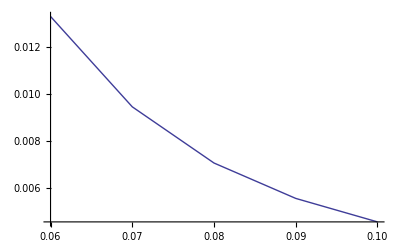

```mathematica
x=-0.05;
m=0.05;
Clear[a]
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,0.06,0.1,0.01}],Joined->True]
```

# Plot

## mapping functions

Mapping functions

```mathematica
setr[x_,a_]:=(1-Exp[-2 √((x-a)^2)])/2
setR[a_,m_]:=(1-Exp[-2 √((a-m)^2)])/2
setχ[x_,m_]:=(1-Exp[-2 √((x-m)^2)])/2
```

## parameters

Parameters

```mathematica
trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;
```

## plot

Part::partd: Part specification temp ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification temp ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

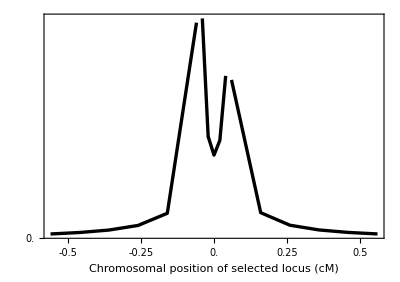

```mathematica
x=-0.05;
m=0.05;
Clear[a]

xplotmin=-0.5;
xplotmax=0.5;
xplotinterval=0.25;
yplotmin=0;
yplotmax=0.2;
yplotinterval=0.1;

Show[

(*AXM*)
ListPlot[Table[{a,invasionplotAXM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.56,-0.06,0.1}],Joined->True,PlotRange->{0,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0},Frame->{True,True,False,False}],

(*XAM*)
ListPlot[Table[{a,invasionplotXAM[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,-0.04,0.04,0.02}],Joined->True,PlotRange->{0,All},PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

(*XMA*)
ListPlot[Table[{a,invasionplotXMA[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a],setR[a,m],setχ[x,m]]},{a,0.06,0.56,0.1}],Joined->True,PlotStyle->Directive[Black,Thickness[lwd]],AxesOrigin->{xplotmin,0}],

PlotRange->{{-0.56,0.56},{0,All}},
Frame->{True,True,False,False},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,yplotmin,yplotmax,yplotinterval}]},
(*FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[FontColor->White],Directive[Black,Thickness[lwd]]}},*)
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
(*Text[Style["A",14,Bold],Scaled@letpos],*)
Rotate[Text[Style["Invasion fitness of W allele",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False

]

Export[plotdir<>"InvasionVsCentiMorgansAllOrders.pdf",%];
```